```mathematica
LDMdirectory="/Users/tientien/Dropbox (University of Oregon)/work/current/LDM";
```

## plot styling

```mathematica
DefaultPlotOptions =
  {ImageSize -> 350, AspectRatio->1.0/GoldenRatio, Frame -> True, Axes -> False, PlotRangePadding -> 0,
   TicksStyle -> Black, FrameTicksStyle -> Black, LabelStyle -> { FontSize -> 16, FontFamily -> "Times",Black},
   FrameStyle -> Directive[Thickness[0.002]]};

SetOptions[Plot, DefaultPlotOptions];
SetOptions[LogPlot, DefaultPlotOptions];
SetOptions[LogLogPlot, DefaultPlotOptions];
SetOptions[LogLinearPlot, DefaultPlotOptions];
SetOptions[ListPlot, DefaultPlotOptions, Joined -> True];
SetOptions[ListLogPlot, DefaultPlotOptions, Joined -> True];
SetOptions[ListLogLinearPlot, DefaultPlotOptions, Joined -> True];
SetOptions[ListLogLogPlot, DefaultPlotOptions, Joined -> True];
SetOptions[ListContourPlot,DefaultPlotOptions];
```

## Load values

```mathematica
(*
<<"/Users/tientien/Dropbox (University of Oregon)/work/current/LDM/DarkSide/Ar.mx"; 
fsqtable["Ar3sFullAlt"]=Ar3sFullAlt;
fsqtable["Ar3p32FullAlt"]=Ar3p32FullAlt;
fsqtable["Ar3p12FullAlt"]=Ar3p12FullAlt;*)
```

```mathematica
(* Ar 3s*)
fsqtable["Ar3sFullAlt"]={{{-2.4,1.8},{-1,4}},{{0.0005119860812335434,0.0007304121740525511,0.0010371818797372898,0.0014632262826107406,0.002046548717107514,0.0028309885820170877,0.0038623559817940506,0.005180521219339491,0.006806191078639631,0.008722156522938718,0.010851290856843061,0.013037637086646063,0.015041463571800695,0.01656119908789628,0.017290329469959436,0.017002938157298586,0.015641309867005633,0.013365108051976464,0.010528592700164313,0.007583664563816064,0.004946299845895557,0.0028853637716530216,0.0014795944039373518,0.0006495047163022033,0.00023339481683124934,0.00006371787754806617,0.000013752755861497509,8.938927733142629*^-6,0.000015145041224350754,0.000020637707892911524,0.000022697293098957648,0.000021332580306958328,0.000017463896437281402,0.000012462986812680561,7.680211964590974*^-6,3.995847922661852*^-6,1.6670880514545914*^-6,4.872908279716833*^-7,5.979856727127156*^-8,1.2736421439250138*^-8,9.440455345161176*^-8,1.745281309475741*^-7,2.073578071317066*^-7,1.9470357455436682*^-7,1.5743679612278336*^-7,1.1515793300758759*^-7,7.784975628587305*^-8,4.905208361655469*^-8,2.9236159660278503*^-8,1.6691902073583744*^-8,9.161920993363746*^-9},{0.0006236018304726109,0.000889692784401309,0.001263469513491667,0.0017826842316763837,0.0024937546482917588,0.0034502791914484848,0.004708347775139785,0.006316911706958,0.008301648632537472,0.010642035489221977,0.013244387091186968,0.015918591554487296,0.018371858817669857,0.02023533497276146,0.0211335717484388,0.0207892188638155,0.019130444999859775,0.016351464475311075,0.01288498803319908,0.009283755031709466,0.006057060167648345,0.0035345105483917403,0.001813138959898022,0.0007962271394246617,0.0002862103915495248,0.00007812844224488316,0.000016822168442758513,0.000010912175399099931,0.000018523476278951637,0.000025249109054338847,0.000027757962959380186,0.000026074675446475974,0.000021335704873796126,0.000015220637604241122,9.377352778134032*^-6,4.878130286831543*^-6,2.0350476831512173*^-6,5.948674095331555*^-7,7.303477528107691*^-8,1.554643220491127*^-8,1.1518336553619313*^-7,2.129456570529496*^-7,2.529965147226258*^-7,2.3754886565893064*^-7,1.9207556902546173*^-7,1.4049135441207658*^-7,9.497374285044518*^-8,5.984044700449668*^-8,3.566565770061981*^-8,2.0362430198225107*^-8,1.1176478468502745*^-8},{0.0007591521965455252,0.0010831533355021197,0.0015383711593274527,0.00217087996366238,0.0030373794371367896,0.004203418048950109,0.005737712129652938,0.007700429317448235,0.010123503099927647,0.012982592411706831,0.01616401658419343,0.01943609412081827,0.0224411949537085,0.02472799469208535,0.025836306166496653,0.02542528654328172,0.023405274481188995,0.020012388757545428,0.01577525573995329,0.01137020463762841,0.007421086475221229,0.004332229416730793,0.00222335836753679,0.0009768448741024314,0.00035128328762143815,0.00009588145192205116,0.000020581847391895018,0.000013320180256831323,0.000022669376150906405,0.00003091356419103725,0.00003396722409342253,0.0000318826980008611,0.00002606969927755052,0.000018587830780708815,0.000011447738694752755,5.953922116914087*^-6,2.4836695769717075*^-6,7.260753768996051*^-7,8.920806226924104*^-8,1.897153643204391*^-8,1.4050889480651048*^-7,2.597998220329267*^-7,3.086854071805386*^-7,2.8985204049387654*^-7,2.3437760659980784*^-7,1.7144031538433798*^-7,1.1590021461464894*^-7,7.302820594643466*^-8,4.3527023216592625*^-8,2.485132044893296*^-8,1.364063550616727*^-8},{0.000923414648913953,0.0013176144967492942,0.0018716032618474182,0.0026415992876343748,0.003696862646416795,0.005117582912765983,0.0069880139752357025,0.009382236797616156,0.012340153380171474,0.015833184311182625,0.019723675783163756,0.023729504665915686,0.02741385607587334,0.03022424093982183,0.03159600596520728,0.03110941882004815,0.028651801485330922,0.024509710032164612,0.019328975129589667,0.013937695340084884,0.009100881338542135,0.005315317624282709,0.0027292301983345133,0.001199701491089969,0.00043160422958121367,0.00011779136999519294,0.000025208290034565246,0.000016269476933037025,0.000027753061731548614,0.00003786045253527399,0.000041580772637119355,0.00003900368106018225,0.00003187434449577858,0.000022717183360460668,0.000013987033654497376,7.27335289796796*^-6,3.0338052879525376*^-6,8.869267752277663*^-7,1.0903280059334607*^-7,2.3170796129748428*^-8,1.7150614008033385*^-7,3.1710631599442747*^-7,3.767496630649659*^-7,3.5373399214556966*^-7,2.860118130790042*^-7,2.0919629736057333*^-7,1.4141672910941995*^-7,8.910139828101967*^-8,5.3104805379239605*^-8,3.031854462240315*^-8,1.6641006889849515*^-8},{0.0011224361095953496,0.0016017406548260828,0.0022755417412531898,0.003212432185055673,0.0044970295955849785,0.006227480194987203,0.008507179264059955,0.011427485409591655,0.015038448881459075,0.019306827538879284,0.024066194509644995,0.02897313382975925,0.03349403748618921,0.036952112565826756,0.038653819647499296,0.03808156590413806,0.035093154706597955,0.030036064245644513,0.023699529180467478,0.01709806319576876,0.011170492355685794,0.006527812785953545,0.003353901380446739,0.0014752635230005455,0.0005310434902096513,0.00014491169626010473,0.00003088716283724859,0.000019868612136222997,0.0000340072782287918,0.00004641870081121326,0.00005094504076569701,0.0000477399769708205,0.000038978482566061084,0.00002776138943485404,0.000017084922136323214,8.88190331638004*^-6,3.7043848069222294*^-6,1.0830905418548931*^-6,1.3327190440893663*^-7,2.828768694097186*^-8,2.0926328373411796*^-7,3.869678943955535*^-7,4.597771203886841*^-7,4.317012079256267*^-7,3.4906165306766056*^-7,2.553197268430276*^-7,1.726004191927037*^-7,1.0875132438872965*^-7,6.481739729805275*^-8,3.7006066474312313*^-8,2.0311882571282363*^-8},{0.0013632092901519563,0.00194553745114004,0.0027644798315489133,0.0039037258386762862,0.005466684226953644,0.007573558972271459,0.010351393265918314,0.013913109470164003,0.01832182627902281,0.023539442361313154,0.029365219876458366,0.03538140835977727,0.04093600533859557,0.04519926641846956,0.04731808486787854,0.04665256928491112,0.04302202592939674,0.03684706490405299,0.029092455332165854,0.021002248678277366,0.013730211222886219,0.008029271627017736,0.0041284334670448905,0.0018173753891513697,0.0006546303053615077,0.0001786089466939191,0.00003788771727516366,0.000024271619373556687,0.000041707309640006146,0.00005696633231289594,0.0000624716809095275,0.00005847486044930411,0.00004769437926159642,0.00003394294399088983,0.000020878393311037577,0.000010850681011070359,4.524936155968407*^-6,1.3231431933090918*^-6,1.629806792670661*^-7,3.454653175726735*^-8,2.553689246504375*^-7,4.722707965038444*^-7,5.611363219188338*^-7,5.268600949933212*^-7,4.2599732304908377*^-7,3.115911274607284*^-7,2.1063897049361087*^-7,1.327171364867144*^-7,7.910071882635114*^-8,4.5160540144683037*^-8,2.4787571405818285*^-8},{0.001652967636960991,0.002359362131675118,0.0033532449801160504,0.00473666388287048,0.006635963783823072,0.009198405315994985,0.012580247167502012,0.016921388482078106,0.02230191185467351,0.028679103739500722,0.03581174466729092,0.04319238502504546,0.05002458313469986,0.05529048086953679,0.05793924178998923,0.05717769094938391,0.052774411707439316,0.0452370852128058,0.03574495796065777,0.025824747406664343,0.016896148212573767,0.00988877418145509,0.005088965473297976,0.002242221503277188,0.0008082823882345784,0.000220499301619749,0.00004652397520521956,0.000029659700257585243,0.00005119039441975602,0.00006997087424049174,0.00007666613948264607,0.00007167117281275267,0.00005839196297214425,0.000041521066660428606,0.000025525220169802698,0.000013261167153809422,5.5293512864749225*^-6,1.6170203358365296*^-6,1.99412744885034*^-7,4.220470447350617*^-8,3.1169174945408695*^-7,5.764784374775423*^-7,6.849429303214055*^-7,6.430723761566033*^-7,5.199394752353185*^-7,3.802923012650097*^-7,2.5707420698484253*^-7,1.6196992772087677*^-7,9.65333884646902*^-8,5.511220634817319*^-8,3.024930681727721*^-8},{0.002000366914930053,0.0028556286272745654,0.0040596483014786865,0.005736763748698503,0.008041293257633027,0.011153691461796424,0.015266363811318379,0.02055307558552968,0.02711609057438349,0.03490901708258244,0.043643332065663495,0.05270371924647439,0.061117685202600976,0.06763588255081367,0.07096183147738361,0.07010943804992144,0.0647799418067282,0.055583992937007054,0.04396280350433768,0.03179147656755243,0.02081941710276362,0.012196784838017142,0.006283165564799615,0.00277132149820764,0.0009999238466592362,0.0002727424486321754,0.00005719139874585222,0.00003625041890020139,0.00006289052408673728,0.00008604008075765708,0.00009417736670407078,0.00008791142600125945,0.0000715274823686124,0.000050810162178695146,0.000031214528899464104,0.000016210388874377733,6.757925016456061*^-6,1.9765852151800425*^-6,2.4409765502840137*^-7,5.156521740086508*^-8,3.8043242254420964*^-7,7.037012057606512*^-7,8.361079572477209*^-7,7.849668482552479*^-7,6.346436969066624*^-7,4.641788279027148*^-7,3.137744413434183*^-7,1.9768978623106072*^-7,1.1782020059483601*^-7,6.726421942080709*^-8,3.691870103620664*^-8},{0.002414574799650966,0.003447495735827143,0.004902626449733506,0.0069312936670731665,0.009721872967519567,0.013495523158811699,0.0184894260013247,0.024920020232206432,0.03291881780599949,0.042437888934508367,0.05313426116074517,0.06426363091734953,0.07463938162172262,0.0827271437900431,0.08692453471003288,0.08600172791937709,0.07956912237323596,0.06835790494302764,0.05412883824954917,0.039186874586248886,0.02569115579096702,0.015068169512846232,0.00777175245386731,0.003432156289971572,0.001239694113157128,0.00033810574438669264,0.00007039428087407049,0.0000443133038211172,0.00007734693926084361,0.0001059302550115903,0.00011581315757881036,0.00010792121045730603,0.00008767004519840274,0.00006220303031576081,0.0000381828671458152,0.000019819728640150408,8.261019868890314*^-6,2.416640132814079*^-6,2.9894379222653207*^-7,6.300904455011102*^-8,4.643183847683493*^-7,8.590095869945593*^-7,1.020664624744051*^-6,9.582083000202308*^-7,7.746905321024004*^-7,5.666023243344416*^-7,3.830056701660218*^-7,2.413046438521985*^-7,1.4381232701932192*^-7,8.210254176307302*^-8,4.506253125364933*^-8},{0.00290445565510032,0.004147692538882337,0.005900578703751442,0.008346971020569135,0.01171656906233729,0.016280354766593993,0.022330996733723303,0.03013890052050608,0.0398744722127224,0.05149244453446051,0.06458856458658153,0.07826573153336783,0.09107785045945033,0.1011398865774674,0.10646778490535108,0.10552159189514332,0.09778812739635513,0.08413701442520873,0.06671775344949245,0.048365971599009634,0.03175121836773577,0.018647675395194623,0.009631487469552787,0.004259548061658182,0.0015404646962414515,0.00042010975406748987,0.0000867745834248801,0.00005418215762164243,0.00009522446220879926,0.000130574663283129,0.0001425720907564025,0.00013260027130410323,0.00010752800388658398,0.0000761902853632749,0.00004672644302131239,0.00002424136183948928,0.000010101759306089138,2.9557054291769524*^-6,3.663303927806207*^-7,7.700969912855428*^-8,5.667258854488945*^-7,1.0486548701277173*^-6,1.2460186667672115*^-6,1.1697184096711213*^-6,9.456530764858759*^-7,6.916247145979011*^-7,4.675051818104244*^-7,2.945339737246315*^-7,1.7553197631908335*^-7,1.0020956824820003*^-7,5.499986058226865*^-8},{0.00347827463145091,0.00496810672586301,0.007070816273905448,0.010009249044306261,0.014063043288334206,0.019564030418237,0.026873638610831717,0.036330724838007235,0.04815777884536024,0.062319425736639844,0.07834480305430795,0.09515770653558903,0.11099916753199587,0.12355313897835393,0.1303582287725792,0.1294779226024576,0.12022901827811573,0.10363648261379432,0.0823212222037323,0.05977428792598233,0.03930251453259831,0.02311928234715428,0.011960607815633486,0.005298401067792815,0.0019189590504439368,0.0005233408752795822,0.00010713940774768123,0.0000662597406538396,0.00011737376212461498,0.00016118014741031228,0.00017573427410720125,0.00016308225966458006,0.00013197674830782622,0.00009336798239508038,0.00005720072593587288,0.00002965671468450084,0.000012355360058148521,3.615996984088338*^-6,4.4918470115237017*^-7,9.412910166126143*^-8,6.916888238621663*^-7,1.2802025917931922*^-6,1.5212276573088657*^-6,1.4280443807313642*^-6,1.1544734215623201*^-6,8.443449693159794*^-7,5.707327334414988*^-7,3.595646614012618*^-7,2.142860757682325*^-7,1.2233316559245995*^-7,6.714200435723188*^-8},{0.004140613772909868,0.005915325343843973,0.008423188189804691,0.011933339762930189,0.0167853144976172,0.023384872974662355,0.032178453010668996,0.04359186126871926,0.05791772170684829,0.07514287328507017,0.0947276232600165,0.1153898914180636,0.13499667964075923,0.15070389431966605,0.159452927111977,0.15879756501573422,0.14781784781555032,0.12770625483389753,0.1016517076058691,0.07395389221477429,0.04871656651795673,0.02871003087858289,0.014880904860585605,0.006604582146666721,0.002396051285440931,0.0006535515217607823,0.0001325088385168597,0.00008103664228084568,0.00014482281090046092,0.000199208907522483,0.0002168559409906531,0.00020075142253233268,0.0001620903978569473,0.0001144707474815231,0.0000700452102826867,0.00003629043442754804,0.000015114932243030018,4.424965320520572*^-6,5.511123376097311*^-7,1.1506110276161975*^-7,8.44152065688446*^-7,1.5628854706028593*^-6,1.857297091307696*^-6,1.7435279259739372*^-6,1.4095187463553069*^-6,1.030888315477976*^-6,6.968316770691265*^-7,4.3900865326333423*^-7,2.616320885922639*^-7,1.4936283740440905*^-7,8.197738507726854*^-8},{0.004892704886709899,0.006991031725315497,0.009960579623081334,0.014124884383450286,0.019894746980217516,0.027765274427226885,0.038287787632418295,0.05199873912239316,0.06928567052556452,0.09017728430660843,0.114069562975357,0.13944897777477813,0.16374014648234783,0.18345432983576876,0.19478409488289045,0.19462352030077745,0.18171921466996907,0.15743246498237667,0.12563160052633426,0.09161400046398653,0.06048355823936485,0.03572142854731232,0.018554899332892536,0.008252891757413866,0.002999754782124978,0.0008184809897874621,0.00016425622736458115,0.0000991417147850445,0.00017888034859415834,0.00024652510342869236,0.0002679265057009199,0.0002473866932059193,0.00019925895694803745,0.00014045571689588177,0.00008583538692550842,0.00004443734628578763,0.000018502567507204634,5.418461696275047*^-6,6.767887381098092*^-7,1.407004899150496*^-7,1.0304376395420121*^-6,1.908397515467135*^-6,2.2680337701273468*^-6,2.1290170393269115*^-6,1.7210876998573092*^-6,1.258731354898858*^-6,8.508227348935618*^-7,5.360093712194865*^-7,3.194331591033095*^-7,1.8235756432609292*^-7,1.0008483679289447*^-7},{0.005726659951202029,0.008183714479406232,0.011667058190413396,0.016563129160374723,0.02336640396281137,0.03267888331895711,0.04518045149192051,0.06154798855438738,0.08229742806678698,0.10752989686607548,0.13659192315454213,0.1677198582419802,0.19782366456808714,0.22263363701113972,0.2374051174504078,0.23817530820283403,0.22321824657411146,0.19404505257190396,0.15532668305104438,0.1135873587428094,0.0751869126729873,0.0445167319382243,0.02318073212580646,0.010335645661834756,0.0037650721975776825,0.0010278743970793007,0.00020404728686543826,0.00012128090032907542,0.0002211454115790683,0.00030544695734202165,0.0003313953091899663,0.00030512776939562564,0.00024510856073794643,0.0001724145443255187,0.00010521547257063887,0.000054424187487162134,0.00002265350454748975,6.6366417267898575*^-6,8.316677610474582*^-7,1.7203985405531689*^-7,1.2576004814747617*^-6,2.330072206401795*^-6,2.7694620038284446*^-6,2.5996687795952945*^-6,2.1015147880895564*^-6,1.5369497905626512*^-6,1.0388727861272107*^-6,6.544700197092793*^-7,3.9002467347077785*^-7,2.2265485116779132*^-7,1.2220063546972802*^-7},{0.006620304792236198,0.009460892801178015,0.013496344296103784,0.019184081888655842,0.02711484128865051,0.038016466203749585,0.05272463238604298,0.07209325530695859,0.09681123015971173,0.12709811130731594,0.16228392606401743,0.2003513610479306,0.23762757529451645,0.26890907138978853,0.2882836488446422,0.290673250951399,0.2736785623056517,0.23890417587187315,0.19195080775261003,0.14084256810672494,0.0935150156971875,0.05552871356772488,0.028995953694541516,0.012964040766112073,0.004734397184545513,0.0012936899907625052,0.00025402342667016207,0.00014834496209670828,0.0002735291887022749,0.0003787532953266136,0.00041023613025998365,0.0003766131605679642,0.0003016748940417273,0.00021173118605484503,0.0001290097250863097,0.00006667146165667781,0.000027742272696318356,8.131288528119784*^-6,1.0227011082270736*^-6,2.103326592964386*^-7,1.5347795162779034*^-6,2.845176340692003*^-6,3.382325768595039*^-6,3.175096096113087*^-6,2.566748033817061*^-6,1.8772659849057313*^-6,1.2689417704282662*^-6,7.994250393533441*^-7,4.7641650561649006*^-7,2.7197772521989657*^-7,1.4927268265665382*^-7},{0.007543099518323824,0.010777390461665228,0.015383278247174547,0.021896245116172323,0.03101544525623151,0.04361448239599238,0.06071567690939973,0.08339455307563447,0.11257160511552868,0.14865185816414758,0.19100811843449195,0.23739122794550196,0.2834901103990821,0.3230001801650265,0.34855990382467644,0.3536340396808201,0.33485808245666265,0.2938112678052899,0.2371454189979783,0.17471082380544742,0.1164266277380312,0.06936646951280849,0.03633762400133289,0.01629675561644336,0.0059684506593898025,0.0016330815087513596,0.00031721274174892746,0.00018147299525210004,0.0003385091913264552,0.0004700672751594736,0.0005083287260905571,0.0004652946838763722,0.00037163634172613166,0.0002602385086379129,0.0001583151522754369,0.00008173953902179878,0.0000340007043027857,9.970693471176338*^-6,1.25900126879545*^-6,2.572368252714901*^-7,1.8735611721318232*^-6,3.475196655287378*^-6,4.131970460781895*^-6,3.8788277401891275*^-6,3.13559786256671*^-6,2.293305068221302*^-6,1.5501583004073883*^-6,9.765782178521505*^-7,5.819835359566404*^-7,3.3224118912516287*^-7,1.8234640989394143*^-7},{0.008438687528358012,0.012049716136598072,0.01720631330736548,0.02452594768899578,0.03482525604462228,0.049141434001497716,0.06871493449729274,0.09489345324940979,0.12890239157860037,0.17142564801585267,0.22197651043298572,0.27814063663046573,0.3349500936577769,0.3848388998062862,0.4186716250322189,0.4280186525611776,0.408136341844516,0.3603584089862881,0.29247256663287563,0.2165227959914889,0.14491322505389334,0.08667581251299372,0.04557036250201465,0.020508671699425066,0.007535495095302192,0.0020657992607332532,0.00039717186902532456,0.00022190155235535263,0.00041885852743820903,0.000583541932761341,0.0006301371903857655,0.0005751040667221722,0.0004579900713336055,0.00031994971492342855,0.00019431993313620818,0.0001002319074620157,0.00004167962062029246,0.000012229999455324511,1.5510058451632222*^-6,3.144933524352381*^-7,2.286885588145853*^-6,4.24501168353399*^-6,5.048646664595994*^-6,4.739747486974705*^-6,3.831742802779376*^-6,2.802589524003336*^-6,1.8944914875010778*^-6,1.1935395156173426*^-6,7.1129482813956*^-7,4.0606947842337464*^-7,2.228695357885127*^-7},{0.009243322650662095,0.013181706981867323,0.018822949154864863,0.026865828828879935,0.038248492452830005,0.05418509072506679,0.07616384140674018,0.10585940009122959,0.14489063745974506,0.19434541066006095,0.2540262797354161,0.3214862931297578,0.39114516986511916,0.4540442859994436,0.4989107192197642,0.5148624788094527,0.4951884655314591,0.44059613216476334,0.36001817926607527,0.26809889424054184,0.18035388307030617,0.10836487542224126,0.057210145001683615,0.025847900753885076,0.009532493587633906,0.0026200632861155828,0.0004991380608545211,0.00027132949207760203,0.0005181119400611099,0.0007244715063106352,0.0007814413275662321,0.0007112658092211186,0.0005648427232238088,0.00039370283327625193,0.00023873436760721338,0.00012302602527813647,0.000051142983487405534,0.00001501660608573968,1.913060829389283*^-6,3.845851340690526*^-7,2.792679050851463*^-6,5.18799982737651*^-6,6.171770093922159*^-6,5.794441390383035*^-6,4.684410157704851*^-6,3.4262738548903527*^-6,2.3161078456886066*^-6,1.459156290537733*^-6,8.695840118316604*^-7,4.964330703509495*^-7,2.7246465272802003*^-7},{0.009873814010587604,0.014046529834684721,0.02004256295134227,0.02863349608675658,0.040873346082309206,0.058155818751982384,0.08223676921471662,0.11516817066800429,0.15905906245345047,0.21555683597745356,0.28496442540877326,0.3650295882061601,0.4497164511594095,0.528630653503196,0.5880063955295641,0.6138393045265734,0.5966465477407311,0.5358885190066602,0.44149544787530237,0.33110859661611397,0.2241002522064581,0.1353635010398646,0.07180217788375653,0.032583559152997425,0.012067414344324635,0.0033283694558377892,0.0006294121534420079,0.0003315712291882363,0.0006399840418031672,0.000898605077396594,0.000968613305792947,0.0008795513503312121,0.0006967054427689254,0.00048459068913798904,0.00029341113615364065,0.00015107145845790455,0.00006278700179521915,0.000018449222285144727,2.3615993169203378*^-6,4.7012842413520995*^-7,3.410851357628508*^-6,6.342379185188662*^-6,7.5476386346122605*^-6,7.086908360456651*^-6,5.72948078939786*^-6,4.19077866265814*^-6,2.832974736881962*^-6,1.784806916475353*^-6,1.0636582397263753*^-6,6.072290904014884*^-7,3.3327538945228826*^-7},{0.010255850315126661,0.014526475162092564,0.020681757133489957,0.029547457301428708,0.0422742812969961,0.06042117476590297,0.08601274495476442,0.12151244515088153,0.1696115109810876,0.2326936673570265,0.3118372920235592,0.40533379619491305,0.5070140865504489,0.6051698151592894,0.6832668730352297,0.7234236752484656,0.7123162178838779,0.6471909673462327,0.5385555686333329,0.4073661873665663,0.27771496016654934,0.1687857037476696,0.0900136123672781,0.04104924459092783,0.015275679756749736,0.004232449278437651,0.0007966689634121238,0.00040494309983798944,0.0007884663666607304,0.0011121988136331504,0.0011988612064234346,0.001086803996473141,0.0008591807948906817,0.0005966053485039868,0.0003608069856589105,0.00018564536043260443,0.00007714537497123624,0.000022685878546717974,2.9176483045078353*^-6,5.745260053418508*^-7,4.167395659828782*^-6,7.756825489486447*^-6,9.233891349734495*^-6,8.670722842730028*^-6,7.009737826308876*^-6,5.1270324488613395*^-6,3.4657805734643126*^-6,2.1833985099976783*^-6,1.3011422818671986*^-6,7.427780791040668*^-7,4.076577779640454*^-7},{0.010346551365840988,0.014546035408729958,0.020612010190769123,0.029394332910045274,0.042104399421543405,0.06042862464241064,0.08663459002581826,0.12359403841891944,0.1746460768622566,0.24308305214405826,0.331081287264777,0.43794981206783135,0.5579251720853935,0.6782892711381261,0.7798340120602364,0.8399847824864795,0.8402456682897923,0.7742234384867908,0.6521473534493712,0.4983949349687428,0.3427108017235312,0.20979300510634974,0.11257250412938485,0.0516213248684601,0.019314869107329966,0.005382880716701174,0.0010121041645525127,0.0004940986011681087,0.0009675694808536407,0.0013718234824441973,0.001480040156371638,0.0013406652478887063,0.0010586197301937143,0.0007343129569033329,0.00044374859208331314,0.00022822500478110526,0.00009483945781670588,0.000027912311161925998,3.606311191864048*^-6,7.014946849814009*^-7,5.092736655268408*^-6,9.489483210549258*^-6,0.000011300459848120393,0.00001061178210672763,8.578423873572541*^-6,6.273901945337637*^-6,4.240758054507689*^-6,2.6714311188947946*^-6,1.5918499626559911*^-6,9.086727488267064*^-7,4.986766073870565*^-7},{0.010164801078212063,0.014117890800589084,0.019828520725070704,0.028131014595456683,0.04024422326651899,0.05791809804265053,0.08358845908439327,0.1204898649918364,0.1726076551925854,0.2442633101287921,0.3390491270972713,0.45786530194305386,0.5961402356918,0.741080259576883,0.8708060963593169,0.9576439648785272,0.9762904590932411,0.9150540903921639,0.7822175924848603,0.6052672318537541,0.42049628058986344,0.2595951521079973,0.14028474956826412,0.06473330391764448,0.024372728115603638,0.006842449331703009,0.001290412675482944,0.0006019156828936955,0.0011806857158274291,0.0016835269705701569,0.001819870321272986,0.0016490039469142805,0.0013017859522811389,0.0009026909607648993,0.000545364318526009,0.00028046005682207424,0.00011656654887585593,0.000034337700242534225,4.456056360203038*^-6,8.548244463601145*^-7,6.219789873633358*^-6,0.000011603653539485782,0.000013823525053062963,0.000012981746633342222,0.000010493245621775849,7.673368257952059*^-6,5.186156282594659*^-6,3.2666235016690055*^-6,1.9462934344105713*^-6,1.1108900508093912*^-6,6.096003311861644*^-7},{0.009824066134631585,0.013394850999990054,0.018532133104555582,0.02600995235215491,0.03699352353033968,0.053211012347375845,0.07716351144708192,0.11233063031160022,0.1632610685149778,0.23532461259932302,0.33376834624506097,0.4616681356430906,0.6166217741894483,0.7868678473149266,0.9489109068845679,1.0697982868688485,1.1161467636499707,1.0678259207653342,0.929039418868111,0.7297212386992243,0.5132416063083783,0.32004931863654923,0.17439505558124607,0.08106038524597589,0.030743694371561187,0.008709473802525701,0.0016538018926267515,0.0007320199676682372,0.0014323670251795329,0.002055805097562524,0.0022289752844231714,0.0020222932490686556,0.0015974137734325383,0.0011080240472842544,0.0006695466612799067,0.0003443876086831002,0.00014318708805133174,0.00004222270149158885,5.504158070925639*^-6,1.0389401813410463*^-6,7.5867047480078024*^-6,0.000014173881502478599,0.000016893423056292393,0.000015865899870138313,0.000012823048638903175,9.375607681406823*^-6,6.3357942302616205*^-6,3.99021655494447*^-6,2.3770825307935555*^-6,1.356604591134342*^-6,7.443562070182314*^-7},{0.009507482336984221,0.012640464943678872,0.017095216933200794,0.02354936803532084,0.03305436692948961,0.04722684830857518,0.06850503523839825,0.10044834767771953,0.14799071526940127,0.21742928968207192,0.3157401278695573,0.448644724512134,0.6169523596058142,0.8115006013349657,1.0087577886551564,1.1711098975641467,1.255720264012342,1.2312776586524157,1.0945414458999452,0.8751446230261246,0.6247450079583718,0.39432600957404723,0.21702448592183232,0.10176017070010816,0.038935445301116096,0.011152306096156127,0.0021379210175879624,0.0008887156727911645,0.0017298324653365706,0.002502844771600007,0.002724120375927812,0.0024757468737419473,0.0019571677506425357,0.001358129805726359,0.0008208964802508431,0.0004223468377697438,0.00017568369892869323,0.00005187245463288666,6.799028812902445*^-6,1.2582259617917737*^-6,9.232457019415673*^-6,0.000017280971629715874,0.000020611334951824387,0.000019362033798939184,0.000015648332566794365,0.000011440295486859248,7.730508526176549*^-6,4.868205443916839*^-6,2.899830365965061*^-6,1.6547864724769228*^-6,9.078936405281346*^-7},{0.009402124265788061,0.01213626314910056,0.01593606970679264,0.02135886624425126,0.029297959708926017,0.04117982229060783,0.05925058345177137,0.0869548804136487,0.12935328090196285,0.19339445355741836,0.2876260897528603,0.42063221978963766,0.5973554568353547,0.8130398781839657,1.046446337660907,1.2569742561791246,1.3918144954873612,1.4051563329007162,1.2814619193981176,1.0472457224958958,0.7610785815703263,0.4873735872512,0.2715256109651283,0.12868689833592148,0.04977223348419072,0.01444786009278622,0.002801636990470588,0.0010778125123613387,0.002082721233487939,0.003045114386656548,0.003329495380762652,0.0030307939334083935,0.0023969454762208134,0.001663319608674927,0.0010053245622697036,0.0005172944430349264,0.00021529414359511523,0.00006367711364286475,8.406675309353116*^-6,1.5178068164587677*^-6,0.000011201169008553785,0.000021019995551683138,0.000025098392770633315,0.000023588464654425615,0.000019067276007551892,0.00001394069008339816,9.420714766819814*^-6,5.9328374073963335*^-6,3.5339747076096454*^-6,2.0166368822129064*^-6,1.1064110379894688*^-6},{0.009638975989901917,0.012094421826359844,0.015389259961195329,0.019954839173819006,0.02650425960154491,0.036220059807417826,0.051047169316956305,0.0741201168158578,0.11031665045410935,0.16681852100658898,0.25331583131622126,0.381087643438844,0.5597800210752132,0.7908515338943911,1.0583940849623714,1.3219165332534286,1.519523291461108,1.5878190738139135,1.4928104372635176,1.2520949402505883,0.9298293528448505,0.6061988246344581,0.34273162704283733,0.16456113926370372,0.06448818179905286,0.01902404273013752,0.0037421287573558074,0.0013080261022733802,0.002500695380261561,0.0037064035200070596,0.004075105502154616,0.0037151227426771567,0.0029379560574726562,0.0020377113591433823,0.0012310813529732075,0.0006334070665412447,0.00026377485651801394,0.00007818886516744602,0.000010419279894471923,1.824617960234425*^-6,0.000013554610599216289,0.000025523023036394958,0.00003052172263684381,0.000028707315392281164,0.000023213451618535876,0.000016975806067552227,0.000011474169173850002,7.227234488950914*^-6,4.305397153222356*^-6,2.457016172187549*^-6,1.3481052981014189*^-6},{0.010251524994374655,0.012595133702801999,0.0156136471372815,0.019624754799053123,0.025165134165007604,0.03315410032196619,0.045166388262581375,0.06386464922288948,0.0936314714509571,0.14141000339205811,0.21730956181475397,0.33468893853642045,0.507865209641566,0.7459241561452498,1.041732208172067,1.3596025964983867,1.631673768515518,1.7740378980563432,1.7293882365862407,1.4963932792272847,1.140476128815903,0.7595579641720234,0.43712021435256854,0.21318813531275213,0.08487024518406726,0.025527889700055328,0.005118860245261335,0.001597036194688796,0.0029896782676405967,0.0045087471351007435,0.004993005435197256,0.004560843637260066,0.0036063519266756688,0.00249956181480452,0.001509207360719653,0.0007763917498224002,0.0003235462666409047,0.000096166157566561,0.000012960746579856272,2.1873074742344473*^-6,0.00001637621584289102,0.000030966645984771,0.00003710257747047686,0.00003493100139072833,0.000028259911126479126,0.000020672560422826067,0.000013976908995037466,8.805694882711774*^-6,5.246444172014474*^-6,2.994378549032245*^-6,1.6430995077628849*^-6},{0.011141484077391168,0.013529068295950103,0.016530936316951204,0.020333415993747196,0.025342494577137338,0.03223390446484601,0.042200069544277866,0.05734220880981255,0.08132427010720121,0.12025031777124782,0.18387874944403002,0.2864663564352711,0.4460794662274034,0.6799074942305044,0.9929600991873562,1.3608822401753888,1.7165025292055074,1.9584860327606188,1.9931478142399148,1.7888863039372067,1.4069062156755494,0.961423597690941,0.5651873210950873,0.2808313532929738,0.11390816402504521,0.03506500999573063,0.0072144329858381045,0.0019746863924481536,0.0035527975013172645,0.0054768295338108825,0.006122950013536225,0.005608812876795477,0.004435621313230875,0.0030722689879200305,0.0018538435058970582,0.0009535529418227758,0.0003977091572232669,0.00011858839033274681,0.000016197510571231687,2.615275107277464*^-6,0.000019757463966430715,0.00003754980492170711,0.000045090700045460724,0.00004249765917904892,0.000034398714575920474,0.000025170414797390762,0.00001702263514211092,0.000010726857299285932,6.391775422467634*^-6,3.648364002165326*^-6,2.0021030927339524*^-6},{0.012116621062259438,0.014671808858861225,0.017786696678831954,0.021698858349687024,0.026608609557810185,0.033031905197348464,0.041823580452932496,0.05452600568686189,0.07394721594044636,0.1050249800081544,0.15626745884474635,0.24137577135010393,0.3802816141252969,0.5971402599171014,0.9111245753355249,1.316703362295518,1.7587464735025082,2.124395924759164,2.2793736563626323,2.144035300273229,1.7521991482216361,1.2346950931705647,0.7449474189398182,0.3785711734932672,0.1570137114130594,0.049678423564754284,0.010563919097916765,0.0025174191485416502,0.004192249557437059,0.0066473451082016575,0.007525240571140482,0.006918976293748459,0.0054725822413681695,0.0037870182402350207,0.002283129102272389,0.001174037662328657,0.0004901231006666755,0.00014670073732418528,0.000020361302215346732,3.118240938636276*^-6,0.00002378309689673973,0.00004547546789491658,0.000054748729773241327,0.00005166051731609345,0.0000418350914170245,0.00003061886547942218,0.000020712083446279296,0.000013053893345707878,7.77876844944727*^-6,4.44017067886676*^-6,2.4366840990346868*^-6},{0.012907795047588827,0.015659626300032602,0.019024217459810557,0.02312605616588101,0.028205354939292052,0.03461092623956468,0.04294434432547377,0.054272437533767204,0.07057251260042098,0.0954545810501769,0.13555057490380376,0.09027522107972392,0.12063833611359154,0.5026458700041354,0.7958385136008355,1.2144925832788913,1.7315292042249975,2.2407322164961108,2.5657179633493645,2.560942772897185,2.1997770866090125,1.6148182796516786,1.0062017991993977,0.5252574589014952,0.22378996336121226,0.07313395723058844,0.01620529375930044,0.0033455718299823085,0.004903684675709637,0.008065069423451454,0.009284401596984033,0.008576981698945293,0.006783260014994523,0.004686754608295119,0.00282146453011035,0.0014499556008006076,0.000605883154196886,0.00018217656948116,0.000025784401624195122,3.707701257408002*^-6,0.00002853744557051828,0.000054970878009947656,0.00006638166149615736,0.00006271861616329806,0.000050813813303231324,0.00003719755482703864,0.000025167116656081362,0.000015863654276450557,9.453089356678528*^-6,5.395789309910142*^-6,2.961071527195709*^-6},{0.013291713173552613,0.016192278380683194,0.01972397506975581,0.02403972294604339,0.02933939219742669,0.03591692434703943,0.044199479090344974,0.0549164296191609,0.06935260963028221,0.08994108540641174,0.12118648681442126,0.17168902460550248,0.257076854305265,0.14207309179229483,0.19970053816650615,1.0428847446665146,1.5937577857055107,2.238513930533235,2.7924401208613685,3.0131666332897504,2.7659396644467686,2.1399678008662204,1.3916402105812251,0.7528506772460483,0.3313299698091406,0.11237926121078305,0.02618774887520494,0.0047840384118314075,0.005669229375073367,0.00976784024915649,0.011506158425880183,0.010699145594864111,0.008459868022965224,0.0058319978194134,0.0035032837881354955,0.0017983849470052618,0.0007521826968404822,0.00022739664789403247,0.000032952945714678775,4.400080236906608*^-6,0.00003411843510100272,0.00006631928535112263,0.0000803756160344647,0.0000760514870950429,0.00006164486699686647,0.00004513322094067455,0.0000305410785570049,0.000019252552251152053,0.000011471839032519461,6.547624331407752*^-6,3.592959692658053*^-6},{0.013138447955227723,0.01605963294422898,0.019639290485707773,0.02403173697097187,0.029433652016212293,0.036102843996072144,0.04439257288450875,0.054865680929682255,0.0683191751522564,0.08624144177023783,0.11148077513453941,0.1493633184991285,0.210576161554978,0.3158716447131182,0.17290339486970283,0.23063256324207032,1.3335769227902725,2.0511567425879207,2.8376254952270927,3.389737221183953,3.4120731195055707,2.84866283644027,1.9604471415896758,1.1112406387008686,0.5094951185294971,0.18081186854298112,0.04472739639849451,0.007591712038940055,0.006463075130324483,0.011771120150686388,0.01432091656184513,0.013445252959691262,0.010632415197696898,0.007308071998223617,0.0043767028487825144,0.002242983646278213,0.0009389697777941502,0.0002856973295940957,0.000042582840049177836,5.219359132945489*^-6,0.00004061277314415551,0.0000798288593717685,0.00009716842905998305,0.0000920942146175359,0.00007468401682100962,0.00005468574147505479,0.00003700949227692699,0.00002333073174825802,0.000013900070503902644,7.932497711476936*^-6,4.352412012754861*^-6},{0.012438244812694007,0.01524721183952492,0.018707212544841104,0.02297534173282341,0.028249573436684182,0.0347816676085378,0.042896909151590265,0.053027583411221296,0.06577619198667957,0.08222872865900971,0.10379954393661545,0.13371305650007373,0.1778739977077466,0.2491877226697508,0.3730527465030128,0.5976899995829,1.0012279435856206,1.6633943780294165,2.579006989967636,3.5129146300875025,4.007216557127832,3.714059422679051,2.7840776783905388,1.6815203063567805,0.8113189636640584,0.3037014331013076,0.0805217984009136,0.013590068630131708,0.007299006601966456,0.014028912284905133,0.017872713397093003,0.017032451394896772,0.013488368965260204,0.009240609633026232,0.0055129981545300865,0.0028188312908480322,0.0011810206767061606,0.0003620719067846563,0.000055772655719784664,6.207952280810764*^-6,0.000048122980718841075,0.00009590784250059468,0.00011735383977107458,0.00011144219792462575,0.00009042008656920266,0.00006621288948898949,0.00004481438884452776,0.000028250279092557196,0.000016827672354247256,9.601314689711567*^-6,5.2671787533496625*^-6},{0.011294243091524802,0.013869604311006065,0.01705403885720144,0.02099945771019093,0.025898382376024584,0.03199559019960306,0.039603540993506846,0.04912368782239409,0.061078511464800166,0.0761664711016611,0.09537098025690252,0.12084493015500922,0.15527562711486195,0.2050070802302976,0.2845938567518486,0.4242364515537305,0.687858231555108,1.1803289452064916,2.018078226649826,3.181127163896113,4.262418527289733,4.590599467169848,3.8869289746456532,2.5685689949606823,1.3332408451328683,0.532312177914747,0.15265144380619225,0.027329996729464883,0.00852921626198748,0.01638968037963803,0.02231324474293479,0.021771365746851748,0.017312610612215187,0.011823878288113505,0.007022392911425695,0.0035798751925199,0.001500972575495624,0.000464212166183711,0.00007427268131276971,7.449002746623444*^-6,0.00005673425841345357,0.00011502472813281602,0.0001416362324033204,0.00013479940140862556,0.0001094234412970412,0.00008012614336364581,0.00005423041647073343,0.00003418146224880842,0.000020353938559941856,0.000011609643917811162,6.367237384720756*^-6},{0.00986087687812196,0.01211831274012948,0.014915432263360532,0.018389988948524658,0.02271813703069898,0.028125982751564256,0.03490460373047142,0.04342945004497191,0.054185394346457055,0.06779986150851706,0.08509041487593089,0.1071469307574875,0.1355080876958476,0.17506142265354474,0.23002651386193887,0.31571357118298254,0.46782841485043236,0.7637892958710264,1.3519768864026096,2.398641595860222,3.84751333421139,5.060372728756133,5.114922068751623,3.8781029226375767,2.228020672167035,0.9647275315711197,0.3027081213502709,0.06021711270178627,0.011383622413097884,0.01849721111003854,0.027704043976114024,0.028058393476846376,0.022522032557524156,0.015350332732163952,0.009071829340053995,0.004607571902772068,0.0019329859083389407,0.0006038642870363716,0.00010087207480621278,9.101197464820951*^-6,0.00006646808385955294,0.00013768039980547423,0.00017083966324534647,0.00016301177737670225,0.00013238691412114682,0.00009692827279305199,0.00006559477596407595,0.00004133409968540646,0.000024601466671991202,0.0000140261986480961,7.689716583243295*^-6},{0.008313963425282438,0.01021596976842339,0.012573536997428702,0.01550403351330073,0.01915842445851308,0.023732101097409305,0.029479337515513772,0.03673249950880066,0.04592720061381919,0.05763450672141273,0.07260097242661015,0.0917973868952622,0.11648125326871711,0.14830021454650277,0.1895513338335728,0.25199131337023195,0.34254390354163267,0.5022996645256408,0.825008697511812,1.5037730602669388,2.795036442551924,4.597193881560136,5.913798689298821,5.512705392248495,3.6938123150221402,1.7926672105286934,0.6250282151613384,0.1418373003898729,0.02066936702047748,0.019795014844212002,0.03385318104661454,0.03637924370216214,0.02974122673800657,0.020293954852742123,0.011935932087619863,0.006036859338855181,0.002533715443797293,0.0008005617091414022,0.00014029404550707286,0.000011495687753911133,0.00007732837333877941,0.00016455988044903187,0.0002061157595523667,0.00019725955745828662,0.00016026982861481608,0.0001173093358427263,0.00007936629704629668,0.00004999124802854621,0.000029734265153308486,0.00001694221911014388,9.283596090457413*^-6},{0.006803028462682694,0.008353223096018438,0.010272864859769398,0.012656642737849699,0.015626583951143986,0.019341125607109374,0.02400766600688668,0.02989986054049091,0.03738139484549751,0.046938283855082384,0.059221732468782255,0.07510258943159642,0.09573545712901442,0.122625074629907,0.1576848084402856,0.2033091038780113,0.2626819789714,0.3655253838177215,0.5292957249828579,0.8678952093666932,1.6352886710096821,3.201358173759492,5.430061973019808,6.797948938530313,5.770249209769133,3.3239198274849557,1.3263078738742922,0.34866850093877383,0.05255028309314972,0.020041019575998933,0.039946027480286764,0.04718237253041193,0.03989022231445667,0.027414392150060703,0.016078749647363954,0.008096553047433112,0.0033995981637331397,0.0010877101473268644,0.00020078842389392298,0.000015323750559518734,0.00008925564387474055,0.0001965617144725741,0.00024904588890182046,0.00023917121202690996,0.00019438923967726805,0.00014220965361127697,0.00009616547155562815,0.000060532691400822366,0.0000359706207809924,0.000020478264376841782,0.000011213187995890945},{0.005427382253725238,0.006657054654118936,0.008176857654928319,0.010060033111237845,0.012400627341823126,0.015320464462004087,0.01897889239447184,0.023586540285156075,0.029424881265627607,0.03687414011296425,0.04645295401921719,0.05887392431015275,0.07511884793241215,0.09653379500055334,0.1249326524261287,0.1626717080735328,0.21262077573229904,0.2779885631581217,0.38450413042897663,0.5517108295756175,0.8970153284063379,1.7373679432609153,3.6008997118792463,6.355091412705691,7.6703039051992565,5.831961201163482,2.819200035073363,0.8802265550536524,0.15997987642915237,0.025806260010552005,0.04396016171194774,0.06040150782387104,0.054173488866100704,0.03791653030791067,0.022270267199822565,0.011182687668670983,0.00469757125363091,0.00152356442943356,0.00029706486189470577,0.000022022082775801398,0.00010203962785064537,0.00023479471759185866,0.00030175118648381353,0.00029096525959341503,0.00023653826589464498,0.00017290210007228342,0.00011682695186685065,0.00007346593304665569,0.000043600108969325075,0.00002479320139697803,0.000013562764605263693},{0.004246879710961607,0.005203076922329234,0.006382033695458146,0.007838720490960604,0.009643228370173356,0.011885744492701772,0.014683334070864716,0.018189925943165104,0.02261041235134556,0.028221436955637922,0.03540210387326237,0.0446796191395429,0.05679689283501526,0.07281089190598983,0.09422953187313281,0.12318401109387729,0.16278673844574615,0.21686876733101942,0.2905000710163034,0.39021350175448144,0.5686762880635298,0.9115780374188217,1.806719523656552,4.002604278275125,7.383258403838276,8.542511242018701,5.65377103474112,2.216848067697651,0.5103183454176343,0.0622906918484297,0.04288386551101301,0.07437820115291668,0.07389698866961023,0.05370259369014772,0.03186542138912357,0.016010104641622037,0.006737085805148941,0.0022169117352611434,0.0004569133089239567,0.00003466155906979713,0.00011546024173629007,0.00028117053816478787,0.00036783098939550436,0.00035639939980810137,0.0002897446808450206,0.00021152517897097653,0.00014274590575580467,0.00008963575579058812,0.000053103054844497626,0.00003014972262742701,0.000016471309209754076},{0.0032735728244880436,0.00400630020274066,0.004907455061789501,0.006017525061906387,0.007387655778083798,0.009082942368316138,0.01118713664535993,0.013808664998630888,0.017090463092258982,0.02122334929717071,0.026466621911790028,0.03317941356502096,0.041869242564932,0.05326775088184014,0.06844847447316178,0.08900609853614673,0.11732128528017899,0.15688460324476677,0.2126195757739154,0.2908641609980121,0.3986481240996818,0.579782111377531,0.9181072879284116,1.8368431100116036,4.386742645247491,8.527078719212112,9.355021153098162,5.260485431672409,1.600971579733059,0.24811631806992893,0.04323512710614862,0.08342438960832109,0.0991432239145928,0.07728263276299732,0.04705816532871333,0.02383201111415818,0.010082668843282443,0.003366451069634812,0.0007322952175041285,0.000059690566099061006,0.00012892251866720547,0.0003379970647951642,0.0004521975574071405,0.0004407659843192172,0.00035828849062786625,0.0002610769376952258,0.00017586010566677222,0.00011020525929529306,0.00006513380559889514,0.000036902002141424116,0.000020124540379510056},{0.0024978823427350945,0.0030542250715474427,0.003736868458015992,0.004575395101398516,0.005606801986302108,0.0068776241484585126,0.008446813075120992,0.01038971667663132,0.012803706323832896,0.015817623512967983,0.019600243550266027,0.02438368733386588,0.030490132820837977,0.03837959078727655,0.04872699394441039,0.06254935262257043,0.08141820044086581,0.10778268243557297,0.14548138239383043,0.20034976950429748,0.2805876195614227,0.3957387084597169,0.5529665869337418,0.91129606505438,1.8347004106867366,4.752873889755056,9.801253077110582,10.059714923770802,4.6498121349571315,1.0354912841748385,0.10558203189809685,0.07657732954490223,0.12506410507883864,0.11089714004237793,0.07111930194102088,0.03674968894659615,0.01571751645023895,0.005338514346799579,0.0012208208341124862,0.00011050081281693954,0.0001415050809077878,0.00040832197698616467,0.0005623003946305278,0.0005524714874060498,0.0004490795899632173,0.0003264114550359827,0.0002193089483988979,0.00013706419904770462,0.00008075648344766312,0.000045625683286389645,0.000024824287579163203},{0.0018979177326385857,0.0023190990555265727,0.002834941744110605,0.0034671354514095396,0.004242563070079422,0.005194669292062833,0.006365262219705507,0.007806927223559732,0.009586329874711587,0.01178884775060568,0.014525249131339032,0.017941621425720103,0.022243134142124924,0.02769432875291093,0.034691212056502004,0.04381406157746654,0.05596198547992656,0.07254586086573916,0.09589365294088908,0.12987058870381896,0.18084896362745181,0.2587859084470897,0.37703917525853364,0.5469093558647867,0.7656183392644731,1.7899854676362155,5.052250137569281,11.220195088212686,10.634097530062233,3.8697248788996377,0.5832878772080372,0.06996981547106483,0.1354855881405842,0.1523480154797531,0.10751925329322219,0.05793140210805336,0.02526712787251438,0.008752305344875788,0.0020958695677125326,0.0002139590693884326,0.00015195187572335735,0.0004957063836440115,0.0007089473888614811,0.0007046232126472169,0.000573301162153666,0.00041547140316979556,0.00027825735569841095,0.00017334729340217,0.00010174498119192164,0.00005728192968422677,0.00003107535363293064},{0.0014400842429643406,0.001759009518837116,0.0021491581813041956,0.00262661388605956,0.0032111872532153436,0.0039273322849751775,0.004805318867650231,0.0058827515706138395,0.0072065680616586435,0.008835720749216208,0.010844863491397924,0.013329570145309716,0.016413977158426598,0.02026241129888471,0.0250978172446102,0.031279295440181404,0.03922321853096748,0.04969280850733678,0.06385411854707966,0.08372221191926077,0.11282524096883348,0.15745538293826697,0.22843421774780456,0.34270157312555205,0.5201097242523537,0.7558816389040094,1.6915595756746205,5.255332424169917,12.834158186885029,10.951755633575756,2.9967918610858777,0.2824331093473489,0.10500380120593694,0.18678917388833852,0.15676541556695,0.09082276014028162,0.04102970797536172,0.014553333145094369,0.0036420062828126723,0.00042132688666319043,0.00015975751312797068,0.0006010477576901193,0.0009038136356260022,0.0009141925013679278,0.0007465433925933583,0.0005396022156999558,0.00036017564371690976,0.00022365542698724324,0.0001307256740318703,0.00007329691943188794,0.00003962816833362863}}};
```

```mathematica
(* Ar 3 p^(3/2)*)
fsqtable["Ar3p32FullAlt"]={{{-2.4,1.8},{-1,4}},{{0.03485144661123709,0.040671030342096536,0.046986328590755536,0.05362318925860404,0.06030298495995907,0.06663033082922583,0.07210001358937868,0.07613570707973093,0.07817009970113312,0.07776451508567783,0.07474484606541108,0.06930578582164533,0.06202349671094921,0.05373861411178917,0.04533204795639178,0.037485243879569766,0.030539945305975248,0.024519386729490618,0.01927633258068665,0.014665378488495267,0.0106426822239819,0.007260635412231002,0.0045940846552841585,0.0026632483579511067,0.0013999380615814442,0.0006641623426766343,0.00028882653890064465,0.0001240218512354011,0.0000623515953799031,0.000041747833294554105,0.00003377853458388113,0.000028616591986370425,0.000023981599143801754,0.000019628846181492384,0.00001559380505951451,0.000011934910899783204,8.748307553779463*^-6,6.126589547542366*^-6,4.1032811217642005*^-6,2.634642007266742*^-6,1.6229697789781539*^-6,9.56504653534631*^-7,5.375999161292797*^-7,2.8908043088973264*^-7,1.5030228462416875*^-7,7.573872661553004*^-8,3.6586279603223547*^-8,1.7017563255068057*^-8,7.72669919594732*^-9,3.4164276451215824*^-9,1.465503002046755*^-9},{0.042430569472408336,0.04952791540547165,0.05723459755950929,0.0653398039953186,0.07350510778508838,0.08124905198086327,0.08795506603961599,0.09291820187207722,0.095442677303629,0.0949881719939483,0.09133671210268997,0.0847213717111698,0.07584315521422795,0.06572883537340783,0.05545674059144186,0.04586273182345826,0.0373675486665678,0.030001848131244912,0.023586919975589312,0.01794548721094178,0.013023967710325855,0.00888625694131035,0.005623714713996557,0.003260996760610152,0.0017147492410225077,0.000813859832209772,0.0003540523356541276,0.0001520055532528853,0.00007632569120520799,0.00005102348895789756,0.000041251256772021135,0.000034940927303952796,0.00002928062387057765,0.000023964742418505216,0.000019036681098710663,0.000014568612589794636,0.000010678020740124573,7.477603159141965*^-6,5.007925814539063*^-6,3.2153813558392042*^-6,1.9806233148207167*^-6,1.1672207636327623*^-6,6.559904887203264*^-7,3.5272341029222243*^-7,1.8338522845983344*^-7,9.24062564805645*^-8,4.4636072212281114*^-8,2.0761189623446243*^-8,9.426245819346714*^-9,4.167812115105698*^-9,1.787784950449774*^-9},{0.051620744207023145,0.06027334408416946,0.06967586608256597,0.07957363102422466,0.08955608149974474,0.09903734320061434,0.10726508706354317,0.11337679935529543,0.11651845071026065,0.11602346425662022,0.1116178320217867,0.10357936230070365,0.09276038264800701,0.0804149131408465,0.0678635651754966,0.05613219204643889,0.045739292095675115,0.03672544841111276,0.02887398510798225,0.021968991091495183,0.015945218841298424,0.01088079729129184,0.0068873461175463935,0.003994920320645267,0.0021015442360553327,0.000997957187364075,0.0004343373939970111,0.0001864414301013071,0.00009347265666863051,0.00006236334241263293,0.00005037384696056762,0.00004266364015300097,0.00003575471791042407,0.000029262604076822728,0.000023241667677298185,0.000017783096563703613,0.000013031609033949587,9.124462939700403*^-6,6.1103141915227185*^-6,3.922999368309687*^-6,2.4164584705816994*^-6,1.4240573257419392*^-6,8.003413792476921*^-7,4.3035348194818537*^-7,2.237566349143804*^-7,1.1275454935861793*^-7,5.4467560783211914*^-8,2.533505188448622*^-8,1.1503360870152061*^-8,5.0863790629753545*^-9,2.1818675133111902*^-9},{0.06274649685663909,0.07329124674915123,0.08476065144486292,0.09684792503493858,0.10905588898528139,0.12067229457950028,0.13077939706641836,0.1383214065774485,0.1422486634111998,0.1417366323596897,0.13643841532174975,0.12668251395693783,0.11350381773279665,0.09843446537877,0.08309314015892805,0.06874123537739718,0.05601964078816074,0.04498282368768996,0.03536824688512803,0.026912573400224613,0.01953593056016617,0.013333677729872992,0.008442293003225272,0.004898650804296106,0.0025781703459637783,0.001224962471457762,0.0005333761565599172,0.00022890655722744197,0.00011458292146237916,0.00007629385167273091,0.00006156244735414794,0.000052124523587032,0.00004367959890370836,0.00003574537306997075,0.000028387770459276742,0.00002171880722224257,0.000015914877843313198,0.00001114288059914465,7.461734118532779*^-6,4.790431417427595*^-6,2.950558223832648*^-6,1.738630745284927*^-6,9.770205560339732*^-7,5.252989302686583*^-7,2.7309738189018314*^-7,1.3760645428897212*^-7,6.646700328692258*^-8,3.0914257875862574*^-8,1.4035773589780134*^-8,6.205803175493847*^-9,2.6619394632112025*^-9},{0.07619742612953782,0.08904261791275153,0.10302991446502072,0.1177908642471766,0.13272446854926,0.14696566914791082,0.159395212679128,0.16872016275614093,0.17364888684577673,0.1731591364323933,0.16680938170348256,0.1549851393556012,0.13894161887006792,0.12055066553737565,0.10179767546418352,0.08423517437334258,0.06865664201995854,0.05513554548465647,0.043354423438914005,0.03299259969445259,0.023952761259095224,0.01635164980969844,0.0103562840307847,0.006011825747315793,0.0031658665802108236,0.001505250685826978,0.0006558174260974651,0.00028138598725096,0.0001405626217243665,0.00009334420988629547,0.00007522606343278223,0.00006368092220234827,0.00005336602821856824,0.000043669781929600494,0.0000346746785996972,0.00002652257335193408,0.00001943078379187578,0.000013602372517334392,9.107761498691425*^-6,5.8468192924006895*^-6,3.6010659625545166*^-6,2.121863875275885*^-6,1.192344195849052*^-6,6.410679412805066*^-7,3.332916688197113*^-7,1.6794093372035454*^-7,8.112092477502693*^-8,3.773068317049046*^-8,1.713095235466866*^-8,7.574462786818651*^-9,3.2490714120943594*^-9},{0.09244026223194976,0.10808278964651098,0.12513947623350288,0.14316952053679088,0.1614480602642373,0.17892565695898693,0.19423753799821136,0.20579921804785478,0.21201846293034615,0.21162363517710625,0.2040484359689424,0.18973995823337322,0.170218170876121,0.14777052102848348,0.12483529759369576,0.103327416031865,0.08423275020692525,0.06765172563128898,0.05320130150619502,0.04049094779439971,0.029401874828048048,0.020076921921381063,0.01272056615226467,0.007388228968138478,0.003893431282023238,0.001852740620081049,0.0008077920397728608,0.00034648990888803835,0.00017266157948895783,0.00011429702073299179,0.0000919689491241776,0.00007783004833303673,0.00006522261744734699,0.000053367175426585556,0.000042366090915678815,0.000032398180979254055,0.000023730540461464436,0.00001660990739804855,0.000011120389206703774,7.138316519421789*^-6,4.396184806216797*^-6,2.5901529764720518*^-6,1.4553680776776234*^-6,7.82438874410206*^-7,4.067785730277586*^-7,2.0496518119343316*^-7,9.900215920713863*^-8,4.6046606712047536*^-8,2.0906391648352907*^-8,9.243664482982372*^-9,3.965044057108466*^-9},{0.11193435924436346,0.1309634658285309,0.15174763534466928,0.1737625048983714,0.19613687895826298,0.21760040368350128,0.2364904899221554,0.2508648306354603,0.2587576638984289,0.2585814746693828,0.24960392313111876,0.23233474740756455,0.2086097639350246,0.18122376994147796,0.15317432658015392,0.1268280231644343,0.10341385315252619,0.08307019530224113,0.06533586647625761,0.04973527202089388,0.036123334714631444,0.024675052555818637,0.015641227172609098,0.009090296959608186,0.0047942883647586875,0.0022836159446575303,0.0009964561216070208,0.00042727127014740744,0.0002123311857896322,0.0001400529597760853,0.00011249200018128174,0.00009516080823978806,0.00007974259959698037,0.00006524029769713886,0.000051780400858560107,0.00003958796768433423,0.000028990935443268102,0.000020288853488618534,0.00001358204210046485,8.717749417942909*^-6,5.368397067038778*^-6,3.1625981190446243*^-6,1.7768026205110409*^-6,9.551612338855673*^-7,4.965442418061536*^-7,2.5018253681721556*^-7,1.2083634015118418*^-7,5.619930191430845*^-8,2.551513835858446*^-8,1.1281083691799244*^-8,4.8388643682994*^-9},{0.13522346763408294,0.15834125391174134,0.18364254258704388,0.2105080559041773,0.2378955588153643,0.2642712345396591,0.28761230623271855,0.3055375631045967,0.31561580873250955,0.315858186788467,0.30530928569693455,0.284536768626304,0.2557499792143334,0.22236230590099101,0.18806328770111802,0.15578372938548457,0.12706122079599977,0.10208778675688708,0.08030980791674089,0.061148452307180495,0.04442676115161924,0.03035965185273513,0.01925541927455066,0.011199088302543748,0.005912117543049993,0.002819216114626146,0.0012313243309014252,0.0005277805049767713,0.0002614433842530163,0.00017172485216114747,0.00013764352778168656,0.00011638672269716208,0.00009752663615677988,0.00007977982213842363,0.00006330354602170088,0.000048383300083257424,0.00003542276616151917,0.00002478536118793451,0.000016589981638690086,0.000010647364911848038,6.555996851635596*^-6,3.861758517928883*^-6,2.1693333743417675*^-6,1.1660710746489482*^-6,6.061550468080701*^-7,3.053965081008963*^-7,1.4749727000369514*^-7,6.859639112870736*^-8,3.114277126193311*^-8,1.376892058433112*^-8,5.905886246893258*^-9},{0.1628673738241327,0.19090126771306107,0.22165860498687348,0.25441493834802426,0.2879307038357543,0.32036087997558044,0.34924894266388434,0.3716760380778143,0.3846304366719011,0.3856098330053603,0.3733565814588745,0.3484796299683239,0.3136271160933362,0.2729650052155084,0.23103826851754825,0.1914860343311878,0.15623993090726065,0.12556826613702388,0.0988089257615876,0.0752579359030346,0.054699766885581154,0.037399156957095954,0.023736141427759917,0.013817206136031518,0.007302386537555327,0.0034867074206579043,0.001524525728629703,0.0006531764789300135,0.00032237166785745836,0.00021071329844767457,0.0001684836387389815,0.00014239430951734004,0.00011931797006288646,0.00009759184506962012,0.00007741264030970447,0.00005914532825106788,0.00004328814528171499,0.000030281622618041685,0.000020265619075558524,0.000013004859165579431,8.006704197732*^-6,4.7156645075328105*^-6,2.648667107827522*^-6,1.4235991871373334*^-6,7.39992081728047*^-7,3.728140398064249*^-7,1.8005072988261458*^-7,8.373342446646705*^-8,3.8014287054874786*^-8,1.680669932763356*^-8,7.208779547699618*^-9},{0.1953778966620849,0.22928589337719382,0.2665990453560247,0.306480755288034,0.34746855688986156,0.38735436693423564,0.4231632355906002,0.4513197743961918,0.4680873932814428,0.4703038675732,0.456297848669936,0.4266845064065191,0.38461674237606724,0.3351726943865937,0.28395809932306726,0.23550374627803852,0.19224787080309216,0.154567857125768,0.12167534115997995,0.0927145225542233,0.06742305143561399,0.046128117261324306,0.029299976095295322,0.017073604110808244,0.00903501882388113,0.0043204091422101186,0.0018913951121905979,0.0008099776561986926,0.00039810948011604637,0.0002587787987203861,0.00020633750221947563,0.00017428449646503678,0.0001460347842423089,0.00011942359093773333,0.00009469669948250488,0.00007232153622011788,0.00005291325338196029,0.000037005185556768026,0.000024760885378627,0.000015887448561888997,9.780120822907985*^-6,5.759210756113752*^-6,3.2342679725798194*^-6,1.7381417654416143*^-6,9.034311640873374*^-7,4.5513068296760683*^-7,2.1979219629688932*^-7,1.0221047063319359*^-7,4.640120015232988*^-8,2.051409935492289*^-8,8.798760351187188*^-9},{0.23317440226096842,0.2740458229545459,0.319183611104881,0.36763837190042137,0.4177030090250147,0.46675299480954285,0.5111999335897384,0.5466705785757305,0.5685235803765911,0.5727454476317403,0.5570938810958691,0.5221243350108162,0.4715573244635417,0.4115711521120717,0.34908613216484696,0.2897596567848676,0.23668481603829458,0.1903951373388722,0.14995709636468812,0.11433120081304227,0.08319892566010018,0.05696681547523798,0.036219747652812925,0.021131292838333857,0.011198851232277264,0.005364206253118957,0.00235167036304022,0.0010065723970248321,0.0004924372654693119,0.0003180776859006606,0.0002528097335563986,0.00021340151422562015,0.00017880999562034847,0.00014619973177378852,0.00011588043994825492,0.00008845642024772549,0.00006469019024996535,0.000045226904213547214,0.000030255603091636778,0.00001941007663116471,0.00001194691499272638,7.034010138823424*^-6,3.949534653090383*^-6,2.122313497343166*^-6,1.1030590367683283*^-6,5.556801308385145*^-7,2.683385128719578*^-7,1.2478227345854427*^-7,5.664732216404649*^-8,2.5043594947819418*^-8,1.0741399113585846*^-8},{0.27637340974001584,0.3253987787218365,0.37977620599840417,0.438454462528588,0.4994701085316467,0.5597335017742275,0.6149420193582963,0.6597614912520644,0.6884247723521216,0.6958166555795087,0.67890455735739,0.6380669445140306,0.5776388684744977,0.5051112286041504,0.4290323556860847,0.3564873679454912,0.2914211022885968,0.23459067020436042,0.1848979426066622,0.14108113570729364,0.10275449847802894,0.07042650306795656,0.044829477824789056,0.026190877217737545,0.013903616807074977,0.006672442318872659,0.0029298179528807226,0.0012533588391270038,0.0006100398575727426,0.00039127907274505376,0.0003098784366404968,0.00026139275240217604,0.00021902545752548058,0.00017904623396366458,0.00014184773813867457,0.0001082165686314651,0.00007910106127671808,0.00005528099044944594,0.00003697209496379388,0.00002371486090982225,0.000014594317623719385,8.591272195484603*^-6,4.823145354066918*^-6,2.5915060428574356*^-6,1.3468759848543194*^-6,6.784943607599273*^-7,3.2763749743463597*^-7,1.523549435919844*^-7,6.916419096714662*^-8,3.0577269510628955*^-8,1.311480250522107*^-8},{0.3248101778407542,0.3832577142866434,0.44842255305124784,0.5191808019079607,0.5933188911819754,0.667246095195889,0.7358451267440841,0.7926371644287878,0.8304593281702057,0.8427684813474552,0.8254289981604173,0.7784461112053459,0.7067782331755672,0.6194662081993232,0.527073228772287,0.43850429525410756,0.35882339535216456,0.28911069309769044,0.22808513170344516,0.17421438727848457,0.12703074407255782,0.08717388113193904,0.055567920892327545,0.032517545492376516,0.01729511878155994,0.00831756397236802,0.003658497372042515,0.0015642019196433134,0.0007571436594944626,0.0004819075035140153,0.0003801260750924532,0.0003203794583485471,0.0002684410407018157,0.0002193907043978096,0.00017372231273197342,0.0001324558980091375,0.00009676908079967111,0.0000676027239090609,0.000045201093823953736,0.000028987651457955444,0.00001783596048105716,0.000010497232137676018,5.891843780614787*^-6,3.165231240886278*^-6,1.644918449872519*^-6,8.285806477951057*^-7,4.0008312939684144*^-7,1.8603213307907297*^-7,8.444941045560639*^-8,3.733355806375633*^-8,1.601223336323799*^-8},{0.3775913863154364,0.44670288422782267,0.5242336389677649,0.6090439910435839,0.6987072226927755,0.7891242852569694,0.8742793741629764,0.9463563336450671,0.996479908747752,1.016262167696,1.0000303764201055,0.9470994869979397,0.8629864615577764,0.7585238839175753,0.6467562245826246,0.5389120362493255,0.44153348280716204,0.3561678403714652,0.2813368768007731,0.21517944463932487,0.15712858291465326,0.1079951605859509,0.0689560331596628,0.04042834707936731,0.021549092997060332,0.010387748960170659,0.004577831152935801,0.001956149223948838,0.0009412257061901624,0.000594021951476253,0.00046648025493921597,0.00039280170863267855,0.0003291172985383443,0.0002689137663259348,0.000212815457759486,0.0001621533044546287,0.00011839463867965496,0.00008267344309286748,0.00005526110611635013,0.00003543170201682576,0.000021796739073374037,0.000012825430311827475,7.196997680308977*^-6,3.865815682426045*^-6,2.0088625111342814*^-6,1.0118589359034377*^-6,4.885519605741566*^-7,2.2715880577004235*^-7,1.0311636393787279*^-7,4.558499976756831*^-8,1.9550936699370468*^-8}},{{-1.,0.1},{-1,4}},{{0.43272716872300226,0.5135437222929146,0.6048697643854992,0.7056468503827596,0.813321483765716,0.9233315980755034,1.028723043303448,1.1201660453176279,1.1867217584430971,1.2176397250857585,1.2051149260610068,1.1472742069009192,1.0499932944787254,0.9261070015808901,0.791688682465485,0.6609348570495044,0.5423490605373531,0.43815292829658836,0.34666268743340345,0.2656138872376117,0.19431782946445714,0.1338115975932459,0.08561106198009136,0.05030144815250845,0.026875737077248635,0.012988443761814267,0.005735752511323757,0.002449623077240351,0.0011713791998342285,0.0007326884141677693,0.0005726525683339201,0.00048175762058756753,0.0004036663980735633,0.0003297478495762108,0.0002607970735817268,0.0001985615186118071,0.00014487832888934678,0.00010111437671512401,0.0000675642242860341,0.000043310369939834954,0.000026638616283362777,0.000015671286666274614,8.792286776508038*^-6,4.722216138000755*^-6,2.4538360352943915*^-6,1.2359907902000213*^-6,5.967625064303197*^-7,2.7747205833312213*^-7,1.2595661425997646*^-7,5.5682781016887775*^-8,2.3882085761863562*^-8},{0.4876566250311843,0.5809167268966456,0.6872126060362607,0.8057146782113048,0.9338953576786293,1.0668521458832845,1.19672657516894,1.3125440440504854,1.4009321297580941,1.4481463803447703,1.443441696741953,1.3829931290451511,1.2726116849272064,1.1272617115690833,0.9666818460274594,0.8088795604777118,0.6649979291042392,0.5382444048287042,0.42673710476772636,0.3277091921881351,0.24031282649936442,0.16588013822935022,0.10638451392123985,0.06266407794182455,0.03357083906286435,0.01626911381377177,0.007200448619821701,0.0030736057448033077,0.0014603490920723427,0.0009048373252710972,0.0007035751804723095,0.000591256864281871,0.0004954040597008012,0.0004045767276870572,0.00031977556822884474,0.0002432807732677977,0.00017738735452702247,0.0001237405031195641,0.00008265452933086091,0.00005297109092001129,0.00003257362481662097,0.00001915803449534428,0.000010745817215006621,5.770450525160837*^-6,2.9982968988591228*^-6,1.510156776648718*^-6,7.290908750744291*^-7,3.389825201305217*^-7,1.5387461348987565*^-7,6.802323763636971*^-8,2.9174264043535778*^-8},{0.5378615126183002,0.6436083123157733,0.7653480007657354,0.902689258630005,1.0533743298207272,1.2124029144021329,1.3711831293921903,1.5170863275728936,1.633992696991892,1.7044621631262895,1.7137701654711217,1.6550174581100057,1.533161669232234,1.3652112155395422,1.1752365343315123,0.9861145143618021,0.8125490592395214,0.6591916265653449,0.5239952855128069,0.40355780688209014,0.29681500893752705,0.2054843548855684,0.1321632749852535,0.07807289716705745,0.041949939066266394,0.020390668555873907,0.009045978546326331,0.0038597514439272862,0.0018219875660577343,0.00111792572607945,0.000864615957344591,0.000725803186993405,0.0006081630037252077,0.0004965390492229718,0.0003921978434672207,0.00029812934976086107,0.00021721469172255274,0.00015143561104357991,0.0001011151804294047,0.00006478626266935808,0.000039831529226327575,0.000023421870157022132,0.000013134823356793521,7.052551507465718*^-6,3.6643986657020774*^-6,1.8456716248044993*^-6,8.910739205568463*^-7,4.142952306154315*^-7,1.880640409944418*^-7,8.313888440752434*^-8,3.565773829258495*^-8},{0.5783734063394583,0.695784834808758,0.8325253227764288,0.98891316314151,1.1633076142785073,1.3510042360364056,1.543040468528657,1.7253254943726808,1.87882017737113,1.9816748917878413,2.01389768709986,1.9639135127533531,1.8344778453049142,1.6441663828192297,1.4220123312771806,1.1971087204952415,0.9890252274436347,0.8045671855266994,0.6416041501885027,0.49591260172804563,0.366100921909301,0.2543720267944911,0.16417371576932724,0.0973067669633611,0.05245773470807199,0.025580379392417037,0.011376743222973999,0.004852616075603532,0.0022759532711616277,0.0013826718126056083,0.0010633961716184051,0.0008915716083570186,0.0007470373655567285,0.0006097593552901842,0.000481313030058799,0.00036558272187277855,0.00026617249752114165,0.0001854684617648451,0.00012379467595089523,0.00007929824683353134,0.00004874349778075987,0.000028655309649022087,0.00001606566494814207,8.624711956465935*^-6,4.480896605051166*^-6,2.2568164404698878*^-6,1.0895110846906627*^-6,5.065314394613363*^-7,2.299269268631799*^-7,1.0164367237858772*^-7,4.359362430192562*^-8},{0.6027125296700849,0.7296470674188229,0.8794490568646837,1.0534648355619887,1.2511207708673286,1.4685824684351005,1.697408296198035,1.9221612383307867,2.12119614980285,2.2676960247662854,2.334953697511053,2.303985536392567,2.17443138327083,1.9646342904979603,1.708948400816224,1.4442822956757733,1.196874073044094,0.9767651992208651,0.7819294076850968,0.6070508907315431,0.45021406002376696,0.31420678639186217,0.20363049648670478,0.12115767126383972,0.06555442417129287,0.032076470285591505,0.014303262736991453,0.006099693809518689,0.002843224467323124,0.0017105098204130405,0.0013081568978069373,0.0010954119324834575,0.0009178082073665613,0.0007489658725904718,0.0005908285245276366,0.0004484232426218391,0.00032626034860936656,0.00022721767162800854,0.0001516074915833004,0.0000970920299610101,0.00005967008652440193,0.000035071410887228115,0.0000196585512651582,0.000010551909527532697,5.481791453617222*^-6,2.7608461871852853*^-6,1.332795396082064*^-6,6.196170172321411*^-7,2.812538197112006*^-7,1.2433277245830668*^-7,5.3324271799053175*^-8},{0.6049284493467227,0.737781987996432,0.8969431358542052,1.0852122242600195,1.3034665177238003,1.5495490443132365,1.8159624590374221,2.087726833641022,2.340956620600973,2.5437982188282016,2.661505755920996,2.6662113026682372,2.5487364308975238,2.3260425048626887,2.03693022055694,1.7293891299044846,1.43798211735894,1.1777003517666016,0.9470218766620585,0.739155204443843,0.5512882544838998,0.386838534445849,0.2519432724805889,0.15056978133970914,0.08179661818439217,0.04016826098811703,0.017959480801281295,0.007658611397686667,0.003549826569930816,0.002116170691763255,0.001609593316732731,0.0013459870705254502,0.0011275932756441938,0.000919932812894826,0.0007253299705866317,0.0005501817183760785,0.0004000878008799407,0.0002785233522690799,0.0001857900480516189,0.00011896045507098292,0.00007309666851578096,0.00004295305164812424,0.000024070034920783755,0.000012916845955536436,6.709349097289677*^-6,3.3787296918504636*^-6,1.630903546859504*^-6,7.581266653981736*^-7,3.440971377227008*^-7,1.5210422807001342*^-7,6.523135281380065*^-8},{0.5808029118510731,0.7145768365682074,0.8775852083503989,1.0741391454302953,1.307339965502986,1.5774163851843936,1.8792811761472177,2.1995121068654067,2.5136329815675764,2.785541623291352,2.971710415545115,3.0319763514166036,2.945168653529311,2.722086068603402,2.405515974780169,2.0532199099124457,1.7132096681253874,1.4078829933283201,1.1377943768207528,0.8936399814543711,0.671049059447741,0.4739662508957347,0.3105066521328486,0.18651910593812393,0.10177453422065365,0.050166976501459765,0.022490598415049263,0.009592192570106295,0.004424405827345198,0.0026161383441986974,0.0019798832716556346,0.001653305829086898,0.0013847098443321819,0.001129450660174651,0.0008902117826260211,0.0006749932129131151,0.0004906916055316947,0.0003415152709899717,0.0002277699864023666,0.00014582059153200029,0.00008958816820643548,0.000052632736826867695,0.000029486356641134633,0.000015819135519218184,8.215080537159053*^-6,4.136321188535897*^-6,1.996281778995629*^-6,9.278263300774951*^-7,4.210651299971316*^-7,1.8610804193972485*^-7,7.980693828698925*^-8},{0.5297496037294092,0.6584863658481913,0.8183428508895824,1.0153251732770807,1.2549562979074969,1.5406530728613854,1.8710509871789833,2.2362336500193334,2.613506869343432,2.964624350564239,3.2378497593162714,3.3784659046023036,3.347970171527607,3.144486701979909,2.810006542048597,2.414116982745356,2.0216765910359946,1.6674072067035866,1.353976882487938,1.0709600349602302,0.8106299357212174,0.5770240854730171,0.3806514417911383,0.2300020788709507,0.1261143952617521,0.06240976441109684,0.0280552750412438,0.01196914537866149,0.005498249325275708,0.003228417555438464,0.002432274128756382,0.0020281557963612857,0.0016980536211255173,0.0013847746613581406,0.0010912700402165429,0.0008273407547323184,0.0006013933537435905,0.00041853898138369196,0.00027912629149860616,0.0001786887363149505,0.00010977081842938703,0.00006447873313438773,0.000036113277443977905,0.00001936836469181764,0.000010055378552770972,5.061802233950552*^-6,2.442443393712641*^-6,1.134950786371771*^-6,5.14967989254246*^-7,2.275794316079062*^-7,9.757804441446945*^-8},{0.4570053675393054,0.5749709688201954,0.7245299364033246,0.9132352268216046,1.1490770156590004,1.4391021420341583,1.7867857656021118,2.1877893322729802,2.6242970706801043,3.059515060576521,3.436140611940335,3.6843619347056564,3.7429826135349074,3.5883941811467377,3.253721731827689,2.81842965582224,2.368996491091188,1.9589808330195393,1.5983932890827528,1.2733652837444103,0.9722162492849991,0.6983193586796703,0.46441398288571256,0.28252754617951853,0.15576869526162532,0.07741483783185359,0.034899788439807525,0.014895351700085074,0.006817122452862692,0.003977049455287997,0.0029834297203113385,0.0024839269757354573,0.002078677461527407,0.0016949015640256655,0.001335641257368838,0.001012693688070356,0.0007362113894838399,0.0005124139027049046,0.0003417493335202367,0.0002187791711416359,0.0001343922420548496,0.00007893038691673147,0.00004419614363744198,0.00002369521349081449,0.000012297540611021453,6.188847547944474*^-6,2.98555380162357*^-6,1.3869652708097104*^-6,6.291735270836213*^-7,2.7800023253927197*^-7,1.1917748620528563*^-7},{0.3723289791008284,0.4751601313980114,0.6085130102212751,0.781093394572463,1.0030361606652949,1.284972511979051,1.6358041120842137,2.058486458188366,2.5433963932604504,3.060083279309758,3.5508971639019054,3.933545410999161,4.120529515537472,4.055624809653394,3.749654413881742,3.284721392379765,2.7726162847725435,2.2957148855052343,1.8786676710860732,1.5065238217512942,1.16112877871221,0.8421739709806185,0.5653180743842251,0.34663653605003686,0.1923394492125953,0.09606476057146908,0.04344999773731289,0.018553304667872764,0.008454724271836613,0.00489526215922102,0.00365383946451142,0.003036915395874696,0.002540338597589314,0.0020710679890723373,0.0016320382663271356,0.0012374798498505264,0.0008996827076228908,0.0006262220315728086,0.00041766481514868406,0.00026738384402908604,0.00016424992914240027,0.00009646044050703438,0.000054002461838159894,0.000028944672006376797,0.00001501772683323073,7.5563332670840905*^-6,3.6446332295568652*^-6,1.6928000586239142*^-6,7.677681660496114*^-7,3.3919173570772557*^-7,1.4539158462272391*^-7},{0.2865214094388142,0.3718305376199525,0.48516241975313773,0.6357880587343319,0.8353102764639185,1.0973296819884544,1.435971367462456,1.8623309507142523,2.3792863297440623,2.966239230704596,3.573767788242655,4.11404363431354,4.47379516743204,4.5534882796603595,4.322182473598836,3.844056015494021,3.26512685650288,2.7036952643263135,2.213045482876322,1.7826926617484764,1.3859482617332441,1.016057152823233,0.688902449253456,0.4262766245004161,0.2383191383610667,0.11974279478351416,0.05437904976545309,0.023231716300334042,0.010524622060995074,0.006030475431745542,0.004470417556568745,0.0037080548079477713,0.0031008160675276377,0.0025278081846809596,0.00199161250799016,0.001509779350464759,0.0010973986581594762,0.000763697669515538,0.0005092995192497733,0.00032604234553036216,0.00020029334204721362,0.00011763239393034778,0.00006585201498357004,0.000035290940957233425,0.0000183080435859607,9.21159893685027*^-6,4.442988764715006*^-6,2.0634567073634407*^-6,9.358091316898362*^-7,4.134175433105963*^-7,1.7720123170347877*^-7},{0.2084528139305228,0.2758063296365085,0.3675469063897867,0.4928174093173546,0.6637426194898758,0.8957366780953534,1.2075589023958673,1.6174686311663735,2.1395966779411477,2.772206558679542,3.482158687841027,4.189023815294403,4.763119181414525,5.0569378569189976,4.974357605532104,4.539674742480754,3.8983989182024246,3.2278581535352506,2.630833969526324,2.121295578526165,1.6603181739300228,1.2297537373688117,0.8432120431993629,0.5270281646361507,0.29716204417167313,0.1503724145601181,0.06862470130062245,0.029333280984561855,0.013185495089980178,0.007448908999921638,0.005470272524545049,0.00452565573899948,0.003783896315470786,0.0030845656902344786,0.0024294171272259382,0.001840654725577817,0.0013371317822708604,0.0009300987349422561,0.0006200982573107826,0.0003969466176107111,0.0002438727382798577,0.00014324454127002652,0.0000801950120327351,0.0023804131541982658,0.00002229586163977619,0.00001121954763520124,5.412327799061515*^-6,2.513796302114664*^-6,1.1400866344729115*^-6,5.037009991896198*^-7,2.1591068215078194*^-7}},{{0.2,1.8},{-1,4}},{{0.14401996012890134,0.1946439518635138,0.2653046301904371,0.36433635275721676,0.5033293311626605,0.6982506392622537,0.9692380510628258,1.3409325957014333,1.8386116692304144,2.4796428048701187,3.256819375045456,4.114283078873114,4.926830563475268,5.508821340717994,5.680598844700167,5.3776633991921425,4.715281986049591,3.921449488114894,3.1828200050834496,2.5553036951050707,2.0040318744259684,1.4975194681928556,1.0382872895401176,0.6560848842355811,0.37357061354381815,0.19054352649029077,0.08743135732515532,0.037390580736272425,0.016647067770500634,0.009238310327268264,0.006702065293864411,0.005525853621910369,0.004619332329163108,0.003765630232949261,0.0029645372840508624,0.002244472554628203,0.0016292356406449212,0.0011325764473669826,0.0007548085821904584,0.00048313394831544934,0.00029685812990207656,0.00017439744052780045,0.00009764688496525272,0.00005233170144519572,0.00002715069930501872,0.000013665400093175196,6.5937715740070735*^-6,3.06287220094888*^-6,1.3892184224463786*^-6,6.13845663651665*^-7,2.6314818175156444*^-7},{0.09611074394937967,0.1325321571607234,0.18446615365797314,0.2589629495160214,0.3661314737888848,0.5204692720246129,0.7421121405251796,1.057836258931941,1.5004775626873634,2.10421208308446,2.8914362945947873,3.8467960775024945,4.888416398822686,5.813980338719392,6.368902213692316,6.351623663067323,5.772238946677034,4.862627864733492,3.9371090566156712,3.1364940848721705,2.4559503766534645,1.8433551034287254,1.291304354047243,0.8251876959017292,0.4747647124000255,0.2442903020139383,0.11279011338943006,0.04824742298920562,0.02123167050289369,0.011524956504363892,0.008229414635962303,0.006753107544314941,0.0056429551956414595,0.0046000581856799295,0.003619806283925308,0.0027384949537609797,0.001986225800420902,0.0013798196050424758,0.0009192119377298593,0.0005882974565364477,0.0003615105909275622,0.00021240890465324666,0.00011893474444054953,0.0000637363556035692,0.000033066763559333936,0.00001664545635450548,8.033180636582653*^-6,3.7316656507256153*^-6,1.6925911586722752*^-6,7.479554348890183*^-7,3.206561562236675*^-7},{0.06433852915199047,0.08976562222932277,0.12652649963565196,0.18008393893339722,0.25851490491807977,0.3738690095217254,0.5437959202576254,0.7935806459100972,1.1579171254749179,1.6806937134574407,2.411374235723125,3.3784479078466148,4.557802174031472,5.810382556104399,6.851494714149502,7.330064772484039,7.048785329348855,6.149837500145965,5.016230009074151,3.9571464666020137,3.077589944737164,2.3146455782245154,1.6321788627334493,1.0546726154283892,0.613506558296634,0.3187207490919158,0.14815350452326814,0.06338121027037341,0.027499282408262868,0.014508757011877678,0.0101393790083908,0.008263527423294373,0.006899671280763855,0.005624211801023065,0.004423336894905825,0.003343431649480946,0.0024227215483813994,0.0016817578116308995,0.0011198160062568046,0.0007165548310326617,0.00044033365799124656,0.000258727317278022,0.0001448515484594929,0.00007760523438354873,0.00004025413387037356,0.000020263871403930224,9.78015629529716*^-6,4.542853610916475*^-6,2.060346222532915*^-6,9.10466473644823*^-7,3.903186104776664*^-7},{0.04573110389504397,0.06334891377748128,0.08882307803654209,0.12601929697866263,0.18085151757775075,0.26235596725086324,0.3843233246106156,0.5676254793504295,0.8432376018579166,1.255344404874472,1.8645760046200286,2.7346581535960293,3.9126553501922237,5.3627864113361685,6.877328608905408,8.057399687846747,8.405144708429388,7.782992389830677,6.517729482406367,5.161927383939547,3.97929431025435,2.978008185745514,2.113731598999285,1.3790573493390512,0.8106716652445549,0.4256435251278737,0.1993847894743806,0.08531420518362506,0.03638918626830352,0.018511697669722445,0.01255722027510214,0.010131162523607311,0.008448184670074221,0.00688585549459674,0.005411784697410523,0.0040857892799637625,0.0029570174338775027,0.002050568013447519,0.001364487008039826,0.000872842361009354,0.0005363156616689333,0.00031507662955162976,0.00017633932449447648,0.00009443046970431453,0.00004896329488368908,0.000024645488641449198,0.000011894481940061487,5.523885346339477*^-6,2.5048084440874323*^-6,1.1067920181696285*^-6,4.7444266678778573*^-7},{0.03632874960993317,0.048860642287647,0.06660585534099644,0.09211495308577439,0.12929742819719045,0.18427804187267385,0.2666645798258647,0.3915860797019679,0.5827797628415361,0.8769444253584834,1.330653619928887,2.0194572037159717,3.0364917111326304,4.453296957705985,6.243257531736708,8.088144569071574,9.387294282640768,9.536606653195651,8.503041798262469,6.887774036350678,5.2900804729684285,3.9498209988134776,2.8057600092765016,1.8490033182758827,1.1007818988236577,0.5841338023938726,0.27611589951218585,0.1182483114006587,0.049482399209105715,0.024068258844512486,0.015672254439659673,0.012457306892458529,0.01036639210648198,0.008448580175799018,0.006634229258555524,0.0050011485859790174,0.0036136754857818507,0.0025025813396056147,0.0016637550181817292,0.0010637497476873898,0.0006534307271414593,0.00038373703474012835,0.00021463529431396469,0.00011485312268644123,0.00005951797549594579,0.000029950607065684637,0.000014452472078670258,6.709591247154516*^-6,3.0415323026555667*^-6,1.3437357128972587*^-6,5.759174754306305*^-7},{0.03237187291147542,0.041885769035423646,0.05482519765602907,0.07273290307996541,0.09801098927093713,0.13438562630200937,0.18784516366791235,0.26805553836338275,0.3907759316703396,0.5817511290798061,0.8837600778963415,1.3622284887233467,2.116320906745937,3.2796468599119573,4.962318038207955,7.131793652190842,9.372289757434112,10.848509285563805,10.72877053834262,9.215669069400912,7.205312220753076,5.381813190526895,3.8334779394844016,2.549599357979469,1.5360583264203735,0.8268885174273478,0.39493114024904147,0.1694157503387438,0.06953012358934102,0.032080534416591436,0.019779918738693426,0.015379639824953212,0.01275521360617673,0.010395141986949023,0.008154775584949642,0.006135739954640372,0.004424277566930021,0.00305855568001132,0.0020308677271141766,0.0012974942317983593,0.0007965896063859252,0.0004674966485810946,0.00026123366072222523,0.0001396379938131908,0.00007230059466624468,0.000036367242482964276,0.000017543078845144448,8.140288259292626*^-6,3.6884170556179934*^-6,1.6290922695087424*^-6,6.980397257915553*^-7},{0.03088039464120082,0.038742068918034285,0.04894743949915881,0.06239565665772193,0.08044289804361435,0.10522051922068097,0.14005920282288414,0.1904561062968452,0.2655561454430523,0.38084525137093445,0.5633549900972407,0.8581113576019874,1.3417429318461964,2.1396722631516942,3.423430850501055,5.373551895419435,8.01076520487583,10.7543565649065,12.373783120745182,11.901337406067327,9.8594345939681,7.483089469325428,5.365520515588541,3.60114517812494,2.207140780428077,1.2052723343598784,0.5835154352117118,0.25169489283210605,0.10141457714330453,0.04416528303674734,0.025375374321196676,0.019101104274822023,0.015754126115954222,0.012840584529030693,0.010063722586224831,0.0075550654712738955,0.005433553295806457,0.003747787261376815,0.0024844425935265095,0.0015855788645253897,0.0009726448300814587,0.0005702357309331628,0.0003182094902238638,0.00016984509130768617,0.00008784035774272697,0.000044155458491393194,0.00002128938951400238,9.87175924668727*^-6,4.470221916000324*^-6,1.9736467889965494*^-6,8.453723825938014*^-7},{0.029860336131527814,0.03680517021675619,0.04550251481497193,0.056489707473130465,0.07053464102655205,0.08877559830086386,0.11300356707509861,0.14601276575616254,0.19253214242526956,0.26066755620510107,0.3649760630217734,0.5310669378204914,0.8057770915746044,1.274548544228533,2.081396938051367,3.4533021863006432,5.677327462133779,8.809821474847077,12.195718174758511,14.027022177213833,13.111890656865604,10.476359208628768,7.6531576704045765,5.218092690924843,3.259811287606433,1.8148852531959505,0.8917997689679358,0.3882862937941197,0.15453281477705583,0.06339323313251126,0.03339459567166994,0.023941026692225194,0.019560171601728838,0.01594646322717616,0.012489483422701153,0.009352864693870052,0.006705511526292212,0.004612032430363409,0.0030508272811954366,0.001944106099520614,0.001191037052885254,0.000697188615666484,0.00038828849923553104,0.00020682888773745133,0.00010679639394230738,0.000053631749121024736,0.000025837849170410584,0.000011968901933807001,5.415194557596422*^-6,2.3895004071160232*^-6,1.0229591506201868*^-6},{0.028252812345531505,0.03454987541444523,0.04228249305473357,0.05180641454628741,0.06359000847546901,0.07836709293214396,0.0969594189722074,0.12081688471706623,0.152285814940498,0.19506071080775925,0.2559027751056857,0.3474797589230816,0.493014213717414,0.7377769863492648,1.1708809864159337,1.9535768270792568,3.3766887130179746,5.82317707978217,9.5403688966639,13.6890796888468,15.780353423302161,14.31809229634115,11.028023077055227,7.723209054450155,4.935917428485433,2.8161035698909473,1.4135238984821217,0.6237536018445576,0.24643946577032824,0.09586389869522367,0.04552599141934063,0.03041161608256956,0.024443613428020396,0.019932695080823414,0.015610764531535853,0.01166046085075702,0.008329130628189118,0.005708481701615478,0.0037655298507857948,0.002394453412367956,0.0014641236744152993,0.0008551068630805603,0.00047494148826132866,0.00025229503530955696,0.00012999279188559862,0.00006519048779578672,0.00003137066479454907,0.000014512282819334657,6.558352851860192*^-6,2.8916589556556565*^-6,1.237056905184884*^-6},{0.025760101673502126,0.03142653285410274,0.03833672595663911,0.04676685909813078,0.05706009477436538,0.06964926559248268,0.08509317783657044,0.10413845237146965,0.12783065391248213,0.15883521778057763,0.19882107382755593,0.2534968577809723,0.3331715545390832,0.4574661005166162,0.6683023860238956,1.0502119229030293,1.780637319212867,3.19055133722068,5.830410046712533,10.147723702366028,15.184759277110707,17.649275224931134,15.521821501727484,11.469622871445265,7.618820409022023,4.495840488581532,2.3200303037445513,1.0423413781470356,0.4134475073067922,0.1538360979513181,0.06540907607721125,0.03951336924450589,0.030817973474634157,0.02512249884843824,0.019697754375429907,0.01468118863765067,0.010443839069785429,0.007127038968758738,0.004684192515867303,0.0029698498421833848,0.0018108855324517985,0.001054218644361938,0.0005833413141448836,0.0003087440273408062,0.00015861850665857134,0.00007939216849503246,0.00003814309749728998,0.000017613216233856794,7.947496673905568*^-6,3.5003933960661246*^-6,1.496039633307164*^-6},{0.02255120438441443,0.02751305540325157,0.03356008981661049,0.04092729755724307,0.04990035683331585,0.06082745173578783,0.07413531225540945,0.09035264327326772,0.11014756417863053,0.13439323595440764,0.16429249406459248,0.20162924516177588,0.2543784683168801,0.3247953983465532,0.430423101593819,0.6068416866821024,0.9308641872696574,1.5806200366850944,2.9313846225034563,5.6788571082807335,10.566607131052981,16.761845593533362,19.648786471105257,16.724002162103716,11.847995077338696,7.360454366743956,3.93907138795744,1.8197315729696704,0.7290156307948193,0.2644714305744448,0.10079324189001207,0.05317130537523197,0.039345624548254375,0.031988323796506464,0.02515808030875031,0.018731728324542455,0.013270226171580246,0.009010453650184871,0.005894755804338452,0.003722273117264081,0.0022605944810989635,0.0013100407675138749,0.000721215939746632,0.00037983663059364445,0.000194384413611637,0.00009703084182013579,0.000046511574339233144,0.000021424913592051006,9.647601102714842*^-6,4.242970008929631*^-6,1.8110651574511224*^-6},{0.018978018452160565,0.023173768189433182,0.028295827531294518,0.034547783137631884,0.042177451655264195,0.05148624522039885,0.0628404888154111,0.07668526336683423,0.09356188347556589,0.11413149821045611,0.13921080275064995,0.16983480596088027,0.20738407447178167,0.2538702613138465,0.32209963882505765,0.4143270436386103,0.5611284739542179,0.8276285671584843,1.3810089204430822,2.614342668167272,5.366325850750105,10.82766683738597,18.35631408125704,21.790940210893414,17.92332148208981,12.094323712404107,6.8976385409816405,3.3206527763481186,1.3575847483025694,0.48810295176546076,0.1700687885394158,0.07595100430113107,0.05122420949553033,0.041205878556335895,0.03259200850090223,0.024295362100075935,0.017153951894945278,0.011584404374743864,0.007535847304913767,0.0047328058130683085,0.0028582457076186127,0.0016460459334364274,0.0009000251934890773,0.00047092185366762824,0.0002397452351897517,0.00011922755022001868,0.000056972349681776844,0.000026157697437915065,0.000011746749864780579,5.155987391124995*^-6,2.1969757204444915*^-6},{0.01540924675351943,0.0188335809688544,0.023022635895707213,0.028148546797825823,0.03442262822408801,0.04210432535450653,0.05151210050506848,0.06303653968256992,0.07715590461705263,0.09445423211808537,0.11564201215336961,0.141579836881869,0.1733077113222764,0.21209148380717527,0.2595264940786991,0.3178251950778591,0.39066644134817424,0.5339071332856744,0.7522774486564023,1.207208632348631,2.2866562814536144,4.944276390350905,10.86579741525452,20.00567870699684,24.168924191481455,19.1192175596557,12.170746000999802,6.2828364752100345,2.672187091828097,0.9674756127741427,0.3178895411681038,0.11900374686533254,0.06884884036390077,0.05379885982941188,0.04289810925656393,0.032166644961209856,0.022678940302791873,0.015239305936386359,0.009849531442402002,0.006143009068441676,0.003682062381982961,0.002102889450159362,0.001139609634795313,0.0005912269725918476,0.0002988916670416209,0.0001478812170872524,0.00007036132139328643,0.00003216402468097416,0.000014391831216563827,6.3002349721166064*^-6,2.6783386902036375*^-6},{0.012066675788884682,0.014758885960123713,0.018058047498169336,0.02210362946109084,0.027068262093860686,0.0331660196073021,0.04066284981927651,0.04988965755730363,0.061258578654751636,0.07528290419168746,0.0926008063361974,0.11400227357088262,0.14045721957071283,0.17314048819465827,0.21344749730357965,0.2629983118133899,0.32366022351071344,0.39775512471209123,0.4891008860715465,0.7036347947187676,1.0683166295317044,1.970432015968286,4.421630195792642,10.66077815058192,21.54451327788566,26.652037872223953,20.376852443263278,12.000345686528448,5.511087256081854,2.0526972154783096,0.6589213998730795,0.21197538827275256,0.09789676585516718,0.07126734979131989,0.057226046986368476,0.04343513569486403,0.03074087245443809,0.02058513199686796,0.013219291352129764,0.008176969414217434,0.004854985943425652,0.002744011557564544,0.0014707023033100934,0.0007548118340072008,0.000378113207800791,0.0001857847894122638,0.00008789036976136042,0.00003994665951548186,0.000017788805140574403,7.759769702959085*^-6,3.2886900005161434*^-6},{0.009054370869258959,0.011079322358820623,0.013563802678154989,0.016614945934278404,0.020366161449056036,0.024984125107002226,0.030677824011148807,0.03771029453994179,0.046413869755480515,0.05720993254087567,0.07063429195694138,0.08736921146845161,0.10828249402634264,0.13447222608309436,0.16731163842715074,0.20864069345000053,0.26037957756321267,0.3250686126401121,0.4057606235535252,0.507096034137812,0.6752018854603729,0.9702604633212626,1.6965162783109269,3.8731052361277456,10.210357237445317,22.974817837807503,29.408262829086894,21.5644016513718,11.626293164131186,4.648430149585351,1.5032356287259208,0.4386412965358331,0.15666429911877874,0.0962884438139507,0.07679181577806075,0.05944461317914375,0.042547874236060525,0.028524036872953542,0.018232522437328414,0.011183289669548867,0.006570160132067809,0.003670420522166872,0.0019430433486863129,0.0009847003517898442,0.00048764543470924406,0.00023747410055519158,0.0001115340959648378,0.0000503266135648639,0.000022273119231721737,9.671450403522414*^-6,4.08263553104226*^-6},{0.006409642534767831,0.007844398230696902,0.009606107326933868,0.011771704260977348,0.014437370353199806,0.017723863103706876,0.021783531097077747,0.026809617119313515,0.03304867858442053,0.04081725593426005,0.05052430257629695,0.06270133414858309,0.07804265696221267,0.09745858013975585,0.12214166257767688,0.15364791802359146,0.19398037440835672,0.24565193159210946,0.3116783719201217,0.395452562171666,0.5006516064971968,0.6325135122356192,0.9023543272093149,1.479281355150234,3.325214065492827,9.531902254260153,24.30274802800549,32.37399620136505,22.721824727345997,10.986407975240994,3.76857141750743,1.055008253149584,0.29848375054827336,0.13649602340803146,0.10245385339339953,0.08119194102529485,0.05937973279879522,0.04019816661019752,0.02565710035443761,0.015639021201521983,0.009101788106473425,0.005031431257806997,0.0026332800995457844,0.0013174155112573608,0.0006439157570373224,0.00031025174760719733,0.00014452514053064902,0.0000646623930820902,0.000028401113516243488,0.000012262933118346779,5.15136024652211*^-6},{0.004168641585894876,0.005101503505197842,0.006247598269978936,0.007657438399319099,0.009394343337645618,0.01153808606418542,0.014189738579428894,0.017478177866343172,0.021568917093108816,0.02667623287432098,0.03307986199869937,0.04114832063744788,0.0513719858182506,0.06440688836398885,0.08114018476495322,0.10277555512381209,0.13094781828293833,0.16786374828567224,0.21644946069141643,0.2804408559741117,0.36427057279332514,0.47252964076114046,0.6091484745433876,0.779554466092006,1.2958232903300124,2.795281662801835,8.652442155790892,25.311401355028604,35.554536080358,23.885043345093802,10.080699790715672,2.903019248201538,0.7106269620121587,0.2205913741288455,0.135368064369447,0.10818197712405714,0.08156012667919443,0.05626106023428087,0.03616714505930934,0.021994910457540737,0.012739317754321048,0.007001275945457115,0.0036388777619826575,0.0018022336448818952,0.0008697101337956321,0.0004143929022892219,0.0001915100338537857,0.00008495267284270897,0.000036994716214547845,0.000015871764861487572,6.630820890873564*^-6}}};
```

```mathematica
(* Ar 3 p^(1/2)*)
fsqtable["Ar3p12FullAlt"]={{{-2.4,1.8},{-1,4}},{{0.08895300036074491,0.08959142134895719,0.08992142643945873,0.08975634025499801,0.08886730557052436,0.08700093989538349,0.08391439766530141,0.07943109510826679,0.07351119439212189,0.06631790912246537,0.05824752905939161,0.049888723148979755,0.04189761505653674,0.03481996617081514,0.02893625337097369,0.024208154593865744,0.020362193594508967,0.01703730199854226,0.013945666169965384,0.010954596095514975,0.008091094456205494,0.005491975251026312,0.0033295972396649837,0.0017338558393887335,0.0007312968373433738,0.0002293894579975449,0.000058898020842503603,0.00004706879207794215,0.00007389422030138222,0.00008605802199535456,0.00007745683586932254,0.00006044079612693953,0.00004585492917000978,0.00003685913526433013,0.00003152740351680596,0.000027109049976185226,0.000022245263299294068,0.00001698642799999961,0.000011972470155615864,7.778039765651019*^-6,4.666161555737924*^-6,2.605371267682338*^-6,1.3728881049434287*^-6,6.886541743352473*^-7,3.2739521973299304*^-7,1.480767829395735*^-7,6.497724791251468*^-8,2.7707650348921342*^-8,1.1441304460427017*^-8,4.614295946155666*^-9,1.8205627833562073*^-9},{0.10756650435343657,0.1083731935322406,0.10881024130197285,0.10865095903279771,0.10761687872320941,0.10539907083112479,0.10170061362237091,0.09630432484517037,0.08915869347429813,0.08045905033003772,0.07068486935190223,0.06055103867271202,0.05085625178747334,0.042266325133740366,0.03512475735398096,0.02938654844007899,0.024719959309306514,0.02068567880351979,0.016933582770795184,0.013302485253619623,0.00982557082313858,0.006669428494827296,0.004043598068836937,0.0021058464168746214,0.0008883723540933095,0.0002788029156376736,0.0000716558204053096,0.000057188709013185594,0.00008970058227218323,0.00010445454314706515,0.00009402411574708652,0.00007338283565835283,0.00005568437726864021,0.00004476262424912938,0.00003828351169077118,0.000032912830695440494,0.000027003855353055947,0.000020618118448645537,0.00001453151836812076,9.440537712001418*^-6,5.663733476510474*^-6,3.1626034815464377*^-6,1.6666976539536824*^-6,8.361486963867809*^-7,3.975849487233221*^-7,1.798589016382404*^-7,7.894062892217744*^-8,3.366995146813414*^-8,1.3906882235178708*^-8,5.61013877856209*^-9,2.2140890613938755*^-9},{0.12978585715992141,0.13081151223245718,0.13139598891135393,0.13126429457314065,0.13007781476615438,0.12746000605467284,0.12304776287099156,0.1165736731744452,0.10797074306999598,0.09747177971489689,0.08565583691330578,0.07338995496493234,0.06164597704547253,0.05123548423744495,0.0425793281874694,0.03562507097675783,0.029970875887618986,0.025082726660052495,0.020535178315205935,0.01613276156223531,0.01191636927924447,0.00808871955912209,0.004904259841038078,0.002554315441665139,0.0010778327290693528,0.0003384861065966659,0.00008710973810627511,0.0000694060828299414,0.00010873220379044345,0.00012659644297355782,0.00011397022996209516,0.00008897396126359249,0.0000675331155317931,0.00005429147657182411,0.000046426266578622274,0.00003990404527807398,0.000032733358736613196,0.00002498944120756177,0.000017611282327178097,0.000011441305230510588,6.864425728930643*^-6,3.833455564847554*^-6,2.0205363867551862*^-6,1.0138574393245399*^-6,4.821999009508523*^-7,2.1819740413165866*^-7,9.579623068024323*^-8,4.087267479291287*^-8,1.6887823111883284*^-8,6.81512438044531*^-9,2.690672850322251*^-9},{0.15623784287046105,0.1575487572079526,0.15833576234843472,0.1582657179272486,0.1569272009743514,0.15386138032833818,0.14862401581600246,0.14088524614041797,0.1305571866078005,0.11791573164291158,0.10365860586008409,0.0888363999512651,0.07463012532565595,0.06202990308229859,0.0515515513644899,0.043134712761028704,0.03629334825792588,0.03037871301254963,0.024874205345595802,0.01954306541395635,0.014435808703365742,0.009799034778628236,0.005941473448707547,0.003094896401405394,0.0013063316122494163,0.0004105711626300431,0.00010582761085269217,0.00008414999742764008,0.0001316387593277256,0.00015323747401012084,0.0001379768259571822,0.00010775058013224442,0.00008181137563388665,0.00006577615115934462,0.00005623705086201294,0.00004832296521021264,0.000039629751884320914,0.000030249449025066086,0.000021316617589016583,0.000013848460472706957,8.309170888959148*^-6,4.640854510820904*^-6,2.446540841454523*^-6,1.227903847233625*^-6,5.841724516112246*^-7,2.6442958281548797*^-7,1.1613607418908711*^-7,4.957073031656961*^-8,2.0490498154758276*^-8,8.272616781657675*^-9,3.2676218990097876*^-9},{0.18753054295160726,0.1892172116068841,0.19028560017076787,0.19033271157792897,0.18885907850801628,0.18530575880225553,0.17912899828029255,0.16992114922757728,0.15756607338477177,0.14238852811016506,0.12522696035610897,0.10735226434969716,0.09019897944887115,0.07497430045996314,0.06231117114923016,0.05214127498500823,0.04387794402523667,0.03673380861322706,0.030082245233651727,0.023636922980044748,0.017460348892903117,0.011852259738050187,0.007186748210966539,0.003744101277294233,0.0015809524265027253,0.0004973813715884111,0.00012846063817312218,0.0001018902273126964,0.00015909605197873513,0.00018515373670446186,0.000166747780693006,0.0001302714078343319,0.00009895029656833869,0.00007956489520051381,0.00006801095282463113,0.0000584195511656017,0.00004789545456986296,0.000036551347471048214,0.000025755042933471933,0.000016731837681692562,0.000010040004017057197,5.60842622964056*^-6,2.957281045519278*^-6,1.4846724400182607*^-6,7.065842948811256*^-7,3.1997381672494193*^-7,1.4059425429892573*^-7,6.003992310253364*^-8,2.4831207571000337*^-8,1.0030505435306304*^-8,3.964235274327183*^-9},{0.22440165312940946,0.2265806920526851,0.22803928849275032,0.2282871746673949,0.22671858211758264,0.22265275093666895,0.21542358569758216,0.20452595616210723,0.18980500708326484,0.1716392959071282,0.15103327539442923,0.12952182448608696,0.10884643960519365,0.09047951414156324,0.07519921021761417,0.06293565412060118,0.052966121936082126,0.04435176178138467,0.036327519351474005,0.028547377187499074,0.0210887262774419,0.014315681019984544,0.008681083916732025,0.004523465525893762,0.0019109329906092226,0.000601927260461637,0.000155833360496812,0.00012322569455558733,0.00019198458782769754,0.00022336204870438542,0.00020120375125433617,0.0001572631857958291,0.00011950731328317605,0.0000961070477819811,0.0000821298598867865,0.00007051897371899728,0.000057795050676052565,0.00004409605098518424,0.00003106779177038466,0.000020183183674217782,0.000012112090975442676,6.767108683175356*^-6,3.569162757600008*^-6,1.7924606945273785*^-6,8.534201089623757*^-7,3.866532075896245*^-7,1.699806510781385*^-7,7.263026557106575*^-8,3.005654796552582*^-8,1.214876974798528*^-8,4.804540577989625*^-9},{0.26737698710397206,0.27021348241693177,0.2722152546710399,0.2727912564728734,0.2712078860251766,0.26663656635333927,0.2582610065789719,0.24545386832454455,0.2280070801454857,0.2063572762569664,0.18170231505781068,0.15589176243298833,0.13103715232316399,0.10893379981875886,0.09053950841452328,0.07578147907499316,0.0637893800826735,0.05342833416807857,0.043771438661147494,0.03440151125835608,0.025414652836644663,0.01725274246202974,0.010462956260475675,0.005453188964984867,0.0023050221130654046,0.0007271623247608098,0.00018882046935579736,0.0001487511994122543,0.0002311064730723389,0.0002687736701332935,0.0002421788870214437,0.00018940056803670426,0.00014401252592293904,0.00011583307535340215,0.00009895513094120698,0.00008492261308428164,0.00006956917673984274,0.000053063931625059104,0.00003738083218294072,0.000024284281683222944,0.000014574847092819468,8.144887937365958*^-6,4.297234060862485*^-6,2.1590114302143304*^-6,1.0284774031646105*^-6,4.6624638155747774*^-7,2.0510470250649075*^-7,8.770049711042401*^-8,3.632064907274495*^-8,1.4692036140154785*^-8,5.8150722947689*^-9},{0.3169977325268772,0.32071065681022143,0.3234688148295789,0.32456154891293065,0.32310198016152875,0.3180823776414327,0.3085019073072466,0.2935794634409085,0.2730337181714378,0.2473605219312293,0.21798137436059448,0.1871189374811601,0.15732991988004302,0.13080291494028745,0.1087188326890586,0.09100703560760155,0.07662242564677531,0.06419600753472161,0.05260621676946723,0.041351205728996046,0.03055056134914751,0.020739874177246174,0.012578927522872327,0.006557859494197857,0.0027739510968393835,0.0008767522332658308,0.0002285202180530247,0.00017919454196494084,0.00027742615260562735,0.000322480455478759,0.00029067069448476845,0.00022748813570883713,0.00017309636799830208,0.000139254366118393,0.0001189164756279116,0.0001019895538141471,0.0000835050667347075,0.00006367055499160045,0.000044844809011393236,0.00002913295352627546,0.000017487346044265288,9.775177812715151*^-6,5.159434379049848*^-6,2.5935419856380995*^-6,1.2362661492655593*^-6,5.608605241181932*^-7,2.4692310431875197*^-7,1.0567350912625307*^-7,4.3804854540110884*^-8,1.7736207494153645*^-8,7.026927919101776*^-9},{0.37363872150894706,0.37852207416944084,0.38233143123774405,0.3842148341487882,0.3831024218082289,0.3777697064591498,0.36698896910547973,0.34978492592321364,0.3257749415829046,0.29551075788193915,0.2606687745899352,0.2239114680063065,0.18832983218121072,0.15659169426138267,0.13015583514704826,0.10896309025573309,0.09176267315758678,0.07690711215341779,0.06304097109664684,0.049561926747785603,0.03661899794222211,0.024860422921259576,0.01507986610345822,0.00786446927614506,0.0033296399889850476,0.0010548810309260056,0.00027624150327589523,0.0002153813168125323,0.00033197425646822656,0.00038563459759684954,0.00034773642066025535,0.00027238814610884457,0.00020744162425572515,0.0001669263619047769,0.0001424779784386012,0.00012210397340107305,0.00009990736837149325,0.00007614318697668506,0.000053618054474940164,0.00003483196786976891,0.000020911791307049552,0.00001169332698917326,6.174864150606661*^-6,3.1059425060116548*^-6,1.481671252504191*^-6,6.728011600382668*^-7,2.964932076884289*^-7,1.2702155330383096*^-7,5.271363461498729*^-8,2.1367641152495416*^-8,8.475810562962257*^-9},{0.43738550930086983,0.44383225509997015,0.4490968016379008,0.45216219245319755,0.45174084954653165,0.44634665274260654,0.43447290890135537,0.4148983995997483,0.38710015132401254,0.3516750213567435,0.3105849225666126,0.2670070565094813,0.22467171603702543,0.18683059176232567,0.15529021919674893,0.13001784471927497,0.10953418106770109,0.09182737634424043,0.0752963386181042,0.059208284669201944,0.043749136210558384,0.029702140872960935,0.01801939566277216,0.009401661602310271,0.003984964890145618,0.0012662589185922191,0.00033355533596941746,0.0002582393512863014,0.000395799887099587,0.00045938098462326607,0.0004144350261534013,0.0003249822740613527,0.0002477601343805526,0.00019943135760645594,0.0001701212793652531,0.00014565772639788771,0.00011908169989300664,0.00009070709292285014,0.00006385652699214099,0.00004148250040847846,0.000024909696771035375,0.000013934600626624424,7.362813894700447*^-6,3.706351566411853*^-6,1.7697861173361924*^-6,8.045157310557698*^-7,3.5495725701193263*^-7,1.5226362854624532*^-7,6.327552221618834*^-8,2.5684356436947456*^-8,1.020284882833185*^-8},{0.5078964547924398,0.5164265538966636,0.5236938066127546,0.5284897404428268,0.5292697710215131,0.5242330909267299,0.5115301810779067,0.48962751146315964,0.45780764941347885,0.41668986482188214,0.3685481392640095,0.3171563832367946,0.26700697260108436,0.22206320552839676,0.1845689853137176,0.154542435428619,0.13023245431106129,0.10922334701156375,0.08959426065531473,0.07046640946279188,0.05207157880876018,0.03535407107278225,0.0214523157476716,0.011199138714884703,0.004753665439920405,0.0015162033611987938,0.0004023653372986281,0.0003088065463809758,0.00046992792116091976,0.0005447937585674595,0.0004917652265855744,0.00038611984762140105,0.0002947510243368089,0.00023734405294806882,0.00020231673723291812,0.00017302655591627626,0.0001413158767243757,0.00010757161304845029,0.00007570412775098365,0.00004917780920551731,0.000029538031579680407,0.00001653197342282467,8.741560015801793*^-6,4.4045268046711205*^-6,2.10559819825388*^-6,9.584429142333445*^-7,4.234724705964522*^-7,1.8193393979138268*^-7,7.572919487435347*^-8,3.079007052637388*^-8,1.2252070981894061*^-8},{0.5842305210581558,0.5955258748261547,0.6055286064788193,0.6128108084527277,0.6155267014897545,0.6114986267829351,0.5984563479538144,0.5744693452619936,0.5385513503087788,0.49130412407082885,0.43533191311487773,0.37509182474092523,0.3159830416034972,0.26283318388355903,0.2184388869650841,0.1829068087861009,0.15417803226579752,0.12935980668517197,0.10615468584318849,0.08350980087320946,0.06171389388670972,0.04190256421606609,0.02543177058060129,0.013286145568448315,0.005649873435921267,0.0018106917963052276,0.0004850647353045618,0.0003682704458983348,0.0005552635059939754,0.0006427283760004785,0.0005805435576751722,0.0004565490514228838,0.000349070214882424,0.000281212970660827,0.00023949990980271944,0.0002045389309435507,0.00016684634399378892,0.00012690034738805465,0.00008927017672486782,0.000057988484631044694,0.000034840760040269,0.000019511855512971168,0.000010326459962508928,5.209113842660398*^-6,2.4937745634435224*^-6,1.1369868532639945*^-6,5.03232979771353*^-7,2.1660685915804557*^-7,9.034084502701074*^-8,3.6804091905975934*^-8,1.4675552362468228*^-8},{0.6649739800317218,0.6799164465404129,0.6936199463621532,0.7044086616040214,0.7100868230765506,0.708027431851268,0.6954443737460382,0.6699012730244167,0.6300406670098605,0.576380974731752,0.5118596355136331,0.44170887029806966,0.37239486153179097,0.3098059393287704,0.25743969311029485,0.2155500014647655,0.18173562586870184,0.15256320879782467,0.12523056033409033,0.0985380004604985,0.07282318618855933,0.04944779813405081,0.030020158457269845,0.015697774541316614,0.006691189791648473,0.0021575750831703544,0.0005849595199056446,0.000438197468599219,0.000652830752955502,0.0007540663583056897,0.0006816065932539142,0.0005370577169221507,0.0004114247340933254,0.00033163248739378316,0.0002821368534469645,0.00024053783838063827,0.00019591304591760252,0.00014885521943573928,0.00010466118575914025,0.00006798307540843822,0.000040860951010067176,0.000022900577417429186,0.000012133166743065934,6.129128070471188*^-6,2.9392896024269797*^-6,1.342759285840931*^-6,5.955571367024444*^-7,2.5692499834188576*^-7,1.074116376516213*^-7,4.3862596937514076*^-8,1.753318699724349*^-8},{0.7482179231340783,0.767935280433744,0.7865944668834068,0.802244153152875,0.812285785094428,0.813559066010817,0.8026456615908732,0.7764632613166704,0.7331424065731884,0.6730146525501233,0.5993282593511138,0.5181783736902267,0.43729280047810065,0.3638571929060148,0.3022708793169146,0.25302646881941976,0.21335398874148595,0.1791718085521677,0.14713779744684002,0.11578702862422233,0.08557361226875344,0.05810921496230889,0.03529305678127919,0.018477729884544547,0.0079004533780298,0.0025676978412437048,0.0007068625041632828,0.0005207850186046374,0.0007638354128308511,0.0008796976867910432,0.0007957762350033234,0.0006284462670807463,0.00048255517043819325,0.000389229813014176,0.00033071147378816194,0.00028136758235854244,0.000228746730132023,0.00017358559523091002,0.0001219726023945521,0.00007922248610809744,0.000047637363365508606,0.00002672250508639484,0.000014176663835839954,7.1734952549470006*^-6,3.4472185955070822*^-6,1.578494137901798*^-6,7.018534156586745*^-7,3.035868573262517*^-7,1.2727349157926477*^-7,5.211740167211839*^-8,2.0892367176966975*^-8}},{{-1.,0.1},{-1,4}},{{0.830875182242667,0.8567821187292263,0.8819964384701328,0.9042678996308868,0.920540999590516,0.9270280765380512,0.9195395647610276,0.8941701563163709,0.8483489101297742,0.7820654758666225,0.698816984002829,0.605638427205196,0.5117353615015819,0.4258835119542532,0.35364570422999686,0.295889368740886,0.2494644492575234,0.20953960714526662,0.17212009145300525,0.13545563108273748,0.1001061045726301,0.06798123077046117,0.04131107149299076,0.021663952220147997,0.009300502761056512,0.003054142442105983,0.0008575433736144527,0.0006188670674061447,0.0008889773412056974,0.0010195365267723529,0.0009229866139967642,0.0007309205398140866,0.000562840035351208,0.0004543647477743958,0.00038544559628568803,0.0003270996604034753,0.00026531946233960597,0.0002010249794705864,0.0001411407932538372,0.00009166330331667083,0.000055147541361927026,0.00003096958352414629,0.000016456241764932404,8.344179607983998*^-6,4.019866845274124*^-6,1.8459568890179662*^-6,8.232412730659361*^-7,3.5723066585163986*^-7,1.5026163980430364*^-7,6.173318128204324*^-8,2.4830402111632458*^-8},{0.9104538740800735,0.9442993974863529,0.9780766267978016,1.0092202303992908,1.0341646358399963,1.0483890540097784,1.0467641648540151,1.024333238047419,0.9775635368682705,0.9058700082074768,0.8128747016392815,0.7066085407855761,0.5980062735175852,0.49780865883107733,0.4131019646306474,0.34533957067057075,0.29100711725329703,0.24441021560826226,0.20077190029812456,0.15800693056665238,0.11675121538787778,0.07928799696122696,0.04821741141168244,0.025341455410744056,0.010938689914958668,0.003641259204995343,0.0010486625414214698,0.0007377221193273997,0.001030628564649385,0.0011748628976762203,0.0010642863932791193,0.0008455609272463908,0.0006533434713546354,0.0005279535659221696,0.00044702446345462805,0.0003781870113601136,0.0003059034436566783,0.00023132858289630438,0.00016225480991458507,0.00010536001247835642,0.00006342757654715282,0.000035666680719881905,0.00001898881786696903,9.652178779573155*^-6,4.663947858714226*^-6,2.1489689161233983*^-6,9.617718558769191*^-7,4.189068353733352*^-7,1.7688785884423176*^-7,7.294851048158055*^-8,2.945494221477276*^-8},{0.9842061126519538,1.0281441681241383,1.0729906583379258,1.1158613007163178,1.152631871456039,1.1779333485209502,1.1854953147669256,1.1690179697281944,1.1236532362834943,1.0478996453007932,0.9452858533452883,0.8248520812998801,0.6995471873406627,0.5825562012602405,0.48298327478622144,0.4031900841014039,0.33936793018247735,0.28484229033991504,0.23389674540605132,0.18401066777365055,0.13592321555055376,0.09231470795920166,0.05619886082677617,0.02962737696863635,0.01288416154494201,0.004367367814207795,0.0012997132777816684,0.0008860751763420126,0.0011919931920902915,0.0013466621388229392,0.0012202379410842382,0.0009731344793091353,0.0007549887240916274,0.0006108265087718998,0.0005160179898819181,0.000434923278720222,0.00035059475805728353,0.0002644917716971397,0.0001852800036386292,0.00012028366453223806,0.00007246404201534905,0.0000408125510591824,0.000021778913639107292,0.000011103191402935234,5.384195286371298*^-6,2.4907438013860087*^-6,1.1193689964193506*^-6,4.896761583308057*^-7,2.0769704919104058*^-7,8.602738193199281*^-8,3.4888498663309557*^-8},{1.0509614388112636,1.107627764546705,1.166654002525101,1.2248532751842178,1.2775065911743477,1.3182753453371512,1.3395078695998182,1.3331846934175258,1.2926539202664868,1.2149890615952408,1.1032538572141766,0.9674327859393245,0.8228143202716323,0.685660974407724,0.5677966801494506,0.4729920330452968,0.39730460087552627,0.3329668261465364,0.2731240304521599,0.21469299748505155,0.15849824384917194,0.10765903367635417,0.06564205582451978,0.034757136830698074,0.015271161070758862,0.0053037753189169035,0.0016460634783261722,0.0010804327907275068,0.0013805346927740422,0.001538653362754435,0.0013934147843244207,0.0011160110347855083,0.0008700220113086139,0.0007049085983267299,0.0005938807706573352,0.0004982880487107013,0.0003999949572129615,0.00030086258305865354,0.0002104146769986001,0.0001365513846573932,0.00008233083447313539,0.000046456043933957245,0.000024858815780880485,0.00001271777749460232,6.192962376829178*^-6,2.878240006707112*^-6,1.2997457416176147*^-6,5.714317110191726*^-7,2.4360849945572083*^-7,1.0139743156112573*^-7,4.132364218001636*^-8},{1.1113823991634917,1.1840737535723014,1.2612146343726283,1.3393620710718082,1.4131884847169784,1.4752649865387804,1.5162762096089006,1.5259973780029716,1.4952948994002861,1.4190561243803403,1.2992547943277586,1.1466082057956724,0.979093214167801,0.8169000341029445,0.67558934445568,0.5611294627146842,0.4697738057405909,0.39258529778327733,0.32133024823494394,0.25218119362356245,0.18599734310533847,0.12636412251818768,0.07722897326084616,0.041152740222601306,0.01834478096581853,0.006583318851529347,0.0021547995668992274,0.001352449597110837,0.0016104719707868789,0.0017575545116550431,0.001587993059417229,0.0012777451785036173,0.0010017202711974029,0.0008129956392853577,0.0006827337288757766,0.0005697188653924966,0.0004549906115697338,0.00034095149364372066,0.00023794329343649665,0.00015432451444910236,0.000093125480982453,0.00005265986703733527,0.00002826944348579404,0.000014521801282398635,7.105686350915109*^-6,3.320124869661396*^-6,1.5075249105361798*^-6,6.665277922987659*^-7,2.8576582715443925*^-7,1.1959002297449285*^-7,4.8999755645160366*^-8},{1.17024968290752,1.2632458876416557,1.3636574687155005,1.4678773682816173,1.5699976843670762,1.6613932721260503,1.73075908687026,1.7656866102174251,1.752510817650068,1.6831725056262683,1.5574424978462336,1.3862007904568927,1.1904719858783643,0.9955794263142634,0.8218390003151168,0.6800878722639639,0.5666144032734577,0.4713272931217987,0.3843319826076562,0.30080214092342356,0.22153175116185175,0.1505742564840497,0.09236527599989532,0.04968299025672164,0.02260694746493432,0.008475951518460206,0.0029619223775487983,0.0017675488092848534,0.0019130903891795509,0.002019604205401211,0.0018142997523336534,0.0014664450146276988,0.0011570176799848301,0.0009408937477233343,0.0007871324303278172,0.0006525397877231692,0.0005178500235300304,0.0003862197522330773,0.0002687645038446862,0.00017413860719420906,0.00010516250947019373,0.00005960779044401514,0.00003211710246172677,0.000016575166236602046,8.154726038963994*^-6,3.833143324633416*^-6,1.7510931110228364*^-6,7.790322165559184*^-7,3.360660376308634*^-7,1.4146133990135657*^-7,5.829249711078113*^-8},{1.2368249988249216,1.3560003305874118,1.4867996990756123,1.625626222279791,1.7660923896904324,1.8983202858350374,2.0094422782074033,2.081578154149501,2.0978126767863783,2.0444241557443235,1.9171112461146418,1.7257162624054605,1.4944433103338228,1.255345882329091,1.0370212404507086,0.8546430009612056,0.7069473197099666,0.5841157729751767,0.4735259188744488,0.369033018937434,0.2712047545743698,0.1845174328207853,0.11385095628674774,0.062105806215365926,0.029094107570434465,0.011551900457492494,0.004360324782922976,0.0024674790034543816,0.0023547470636894703,0.0023571808616254385,0.0020912581271042723,0.001696164578668333,0.001347725605309207,0.00109847059481513,0.0009148115505030947,0.000752368004844823,0.0005923641511038206,0.0004390613638793958,0.0003043069773081211,0.00019681393530194896,0.00011890684992270088,0.00006756473471708094,0.000036552811626632464,0.00001896199279877721,9.384974125757723*^-6,4.440342359069232*^-6,2.041955395108463*^-6,9.145100921043365*^-7,3.97100195277079*^-7,1.681784901916897*^-7,6.971384391302471*^-8},{1.329016314013361,1.483150544210643,1.655002475636342,1.8412868914431797,2.0353792947542457,2.226994851999367,2.398740327846271,2.529763753500173,2.5959371959851976,2.575424542699346,2.4564490373023884,2.245091605199251,1.9681172676508072,1.6664230579350876,1.380256344358017,1.1343713746773083,0.9325135256956854,0.7631297459029984,0.6137300937843168,0.47547631482369007,0.34850885964105877,0.23762062821367153,0.14799445511453346,0.08243068509323724,0.04020254291877134,0.017147601150927356,0.00704463184589419,0.0037911559856987666,0.003094270931904962,0.0028465894222585,0.00246152280634874,0.0019969152835382455,0.001598269300556268,0.0013059812374197441,0.0010817716680692705,0.0008809953531607488,0.0006866105995139437,0.0005046238732203226,0.0003476358815279438,0.00022408031700714317,0.00013530802866985468,0.0000770499534899507,0.000041859815627219417,0.000021832885618956243,0.000010872964494031078,5.179336544495852*^-6,2.398263698631565*^-6,1.0814940820806044*^-6,4.727424257175682*^-7,2.014530250401963*^-7,8.400228597180172*^-8},{1.475832728040513,1.6788958975447374,1.9088377958845484,2.1632504867813656,2.435818108302289,2.7158228753408578,2.982589223307976,3.2098310015225318,3.364108954174332,3.41089821536368,3.324716227863289,3.1017330188716827,2.768105519824287,2.3755885885614756,1.9825598276627197,1.6308369428815745,1.3339671972988356,1.081902780677624,0.8624462686136565,0.6637113263645628,0.4853653491956582,0.3324236191066586,0.2100732345196367,0.12052240438030995,0.06193795244347171,0.02867746818552995,0.01281813353627471,0.006624312095227887,0.004542182992223838,0.0036775812915094486,0.003024813667154015,0.0024356146141432493,0.0019622919818677864,0.0016078359443609498,0.001323004537994944,0.001064000172081422,0.0008178374932224026,0.0005936187532491841,0.0004048887122852155,0.0002592300834052591,0.00015607762398634522,0.00008895896442051368,0.0000485119672566213,0.000025432788812871734,0.000012739148171221623,6.107805713200814*^-6,2.8474506511018266*^-6,1.2927336977683271*^-6,5.687206001556927*^-7,2.4379855809441687*^-7,1.0223685586570572*^-7},{1.716183541498356,1.9901662027938545,2.305380536414748,2.661464664227235,3.053689060335777,3.4722160086381986,3.8938470183501197,4.286448858039845,4.604455252516115,4.793973382402251,4.804642215163476,4.608879845870739,4.221048884804478,3.7018404801692313,3.137149513954951,2.6009419653394277,2.1290509711657797,1.7183326431599872,1.3616256315757163,1.043276526468346,0.7633185913550641,0.5273981613078857,0.34035416623552694,0.2028356925423243,0.11070983729552107,0.0556455600006931,0.026778349809814785,0.01349091434684355,0.007862412204871516,0.005374283259092997,0.0040435849505261546,0.0031812036948336885,0.002573350672148652,0.002114470435249517,0.001725334192242707,0.0013643597734630051,0.0010278627623688493,0.0007313466131158677,0.0004899778582215318,0.0003092983713078747,0.00018462386404292065,0.00010496520728895302,0.000057354163699265494,0.000030178686480389316,0.0000151769380693321,7.313886707313921*^-6,3.430264443200203*^-6,1.566745104185041*^-6,6.931746551668343*^-7,2.987393367115578*^-7,1.259151912418889*^-7},{2.0333429141208783,2.399422759009872,2.828079175421396,3.3234330060198056,3.8855111869419487,4.5070892070098685,5.173278220257923,5.8433836833952295,6.4629772715234965,6.953654057042163,7.224600067531069,7.196974194712871,6.84024637059607,6.20095709949739,5.394574707611645,4.552993766268294,3.765142336894479,3.0520787955042623,2.4251597326447882,1.864737967710559,1.3746641952158973,0.9641463238332063,0.6386985743050857,0.3964726862137194,0.2290709473865129,0.12321902345616782,0.0626648360540963,0.03127559326986836,0.01624062006529932,0.009357264590029517,0.006210256744554277,0.004667038893773151,0.003770523643905414,0.003106213985336836,0.0025091468393196475,0.0019413608300455423,0.001421545978432899,0.0009802541495709295,0.0006363430635349994,0.0003905090679446667,0.00022838371193523022,0.00012852029935216274,0.00007005042591295461,0.000036852115819989205,0.000018524418490369343,8.941710015757581*^-6,4.210642285685431*^-6,1.931592102554223*^-6,8.580096115368118*^-7,3.713126544331445*^-7,1.571410134913553*^-7},{2.013158177849458,2.410898836914382,2.8871763790946146,3.4532108657537464,4.11864620511541,4.888655337316547,5.76392578219789,6.7178814759057905,7.7067758846621555,8.648212421561718,9.420109994334618,9.87503928114279,9.883613098864782,9.400061835280463,8.507940170853175,7.39126840505533,6.235443258132976,5.1447125291519225,4.135933143343753,3.2308168767249246,2.424302223513783,1.7364417215372296,1.1810211786948308,0.7581533502815682,0.45629536213373595,0.2564128426563385,0.13497545697486368,0.0675783741335234,0.033309397932806926,0.017277035285501084,0.010323982327432073,0.007380231231126787,0.005929492359684064,0.004894392433040653,0.003921370376298043,0.00297518470333437,0.002118597514282192,0.001412343362913748,0.000883043839292207,0.0005221513882009877,0.0002963869406531991,0.0001638876084633984,0.0000886753977283612,0.00004643675902176665,0.000023214160575329948,0.000011178070819402746,5.271709451769253*^-6,2.4238229384055454*^-6,1.0787693674870612*^-6,4.68088596471588*^-7,1.986526024737695*^-7}},{{0.2,1.8},{-1,4}},{{1.168219509701766,1.4194938116958964,1.730790163556222,2.1154824816276,2.5896084042458387,3.1702364622031225,3.873222607612621,4.7081848179954795,5.669406300945797,6.721708453493001,7.783125818150152,8.713252767167637,9.346652917102594,9.474514633181615,9.045614741919392,8.14398167596905,7.044030169046697,5.920932786362463,4.864092147013719,3.87460643032689,2.9799199339936693,2.1847326861026124,1.5181554636763825,0.9949213184716602,0.6114428579760858,0.35075957760825666,0.18792485154240002,0.09503987365775153,0.04672162601269674,0.023808883243313612,0.013879071054598907,0.009777187834694473,0.007841104499511451,0.00648071126291214,0.005185275524492952,0.003915130761141539,0.0027670446108235378,0.0018274027142942946,0.0011306432684015737,0.0006616990577300591,0.0003726050217227677,0.0002052176967105615,0.00011099184892078979,0.00005817625744779833,0.000029112959290117277,0.000014045452851766274,6.642820270577922*^-6,3.06328829581913*^-6,1.367080778592319*^-6,5.947293012733528*^-7,2.5302372686736437*^-7},{0.4548363285994128,0.5657054517283748,0.7097865864046878,0.8977644687513854,1.14352603282038,1.4645917524586525,1.8819427424030823,2.4183724335900783,3.0967874648490077,3.9216486599769698,4.872575964346725,5.87472528615556,6.781722899121566,7.389696833475406,7.513365693712948,7.1045039946704085,6.307549362180552,5.362925460456053,4.443562501155952,3.590590046340466,2.812713990684866,2.0967939708623486,1.4798070571733375,0.9802672714467454,0.6070896282782203,0.35059992254209593,0.18931233380770743,0.09690145055227785,0.04861848297222621,0.02551938702576627,0.01530663141916348,0.010940242855779206,0.008800453092170814,0.00727982371169794,0.005841762466118808,0.004435209366765289,0.0031599638141164327,0.0021096945571452666,0.0013234423481750857,0.0007867178988991926,0.0004495129447279991,0.00025027383960280543,0.00013637268983272618,0.00007199622106503402,0.000036331513052639017,0.000017648025566546663,8.382955403052084*^-6,3.880214325521667*^-6,1.737781550704747*^-6,7.579110857837008*^-7,3.2313491017438903*^-7},{0.19175435615457628,0.24795939840400513,0.3245446509684378,0.4294293451594576,0.5735144158515326,0.7715352926049541,1.0433278666619816,1.4126613616931243,1.9075598134496954,2.5543574266652294,3.366130674501604,4.320845064317443,5.341694630501151,6.23913215193217,6.780629236778513,6.7769227532492975,6.231297758335327,5.357458252323598,4.416224570376955,3.544336267289139,2.7688143366558378,2.0839890918600514,1.4815647890165349,0.9865205467136241,0.6124412466874803,0.354567289878291,0.1923325635375327,0.09955307568709146,0.05110379089249701,0.027754276693463035,0.017184362465275313,0.01246682692100711,0.010049744417608916,0.008315747076446842,0.0066946988574569846,0.005115654141215203,0.0036783810002362196,0.0024848857918869935,0.0015809088907659907,0.0009539430492746615,0.0005522404898103305,0.00031022713256651164,0.00016996938472312655,0.00009018429819049433,0.00004577414797219888,0.00002233152168392884,0.00001063218332906746,4.930774405283425*^-6,2.2123425980720894*^-6,9.659828823304437*^-7,4.1221849928860755*^-7},{0.13235831924259842,0.17418182874049978,0.2314920516340803,0.3105556506506735,0.4202060930463288,0.572929376424039,0.7855757446428866,1.080958285369061,1.488087620009814,2.0407948728501992,2.7715694066235486,3.701564144152781,4.79492161662385,5.934784109501055,6.88481389052034,7.344799574680336,7.146688185513369,6.335484403352036,5.223086368367934,4.1299816665897175,3.159099133201747,2.345747847633567,1.656957779824996,1.1040095889804054,0.686874200614433,0.398625982890095,0.2171587560362008,0.11343013051169587,0.059137681844358615,0.03275712360992968,0.0205846992346066,0.014992906858004765,0.01206777278128307,0.00998235049296635,0.008057813056772374,0.006187595814718896,0.0044776704412667215,0.0030476170058235832,0.001955050897799355,0.001189363659865731,0.0006930256798295531,0.0003908166238473215,0.0002145210846025724,0.0001140051168644892,0.000057976481254382443,0.000028314982411796458,0.000013482234665141296,6.252924991456207*^-6,2.805865587721575*^-6,1.2249219846098695*^-6,5.226144434081095*^-7},{0.14081237374844044,0.1810375799032172,0.23459351539989354,0.3065665561510341,0.4041611738504622,0.5375786892482536,0.7214544682099093,0.9756559449149887,1.3277570519832507,1.813654779891395,2.4764775520301994,3.363674957250377,4.49434571713749,5.830280915218696,7.203126964966323,8.305627398755565,8.69305814732518,8.19047924215598,7.008715143239371,5.561968570692945,4.1672092217829935,3.0059538395764225,2.076719441939533,1.364478475508457,0.845925032861405,0.49131314624842143,0.26874125134294846,0.14114391158544493,0.07401716675202748,0.041137774804371786,0.025779867587169117,0.018646331873468345,0.01493123541689353,0.012340500081104332,0.009984019114601929,0.007694892001269038,0.005591135362842189,0.0038210335292325026,0.002460713768205545,0.0015018551430905208,0.0008768727300688092,0.0004947456254841821,0.0002714514580297824,0.00014419203852289496,0.00007330132678522897,0.00003576932134134848,0.00001701155674484102,7.882133285532754*^-6,3.5339216134350286*^-6,1.5413870953771015*^-6,6.571182633629479*^-7},{0.15595082408433747,0.19538671794312387,0.24623937645298527,0.31242844702626166,0.39946800288679435,0.5151921514957057,0.6709715663023031,0.8828054560580624,1.1739224122204641,1.5770497760837214,2.136894899504771,2.9103047994846056,3.9670225302710462,5.341750961292297,6.997554680579197,8.740710330937118,10.052213144804051,10.415484562669151,9.581377270477228,7.947408220954211,6.034363246078241,4.268638292239054,2.8726146487635753,1.8387916630628924,1.1212276388325544,0.645617573046461,0.3525994323665973,0.18523400976892418,0.09694999480253881,0.05341972223719429,0.03298125336460456,0.02349900060088962,0.0186623220888407,0.015403249558208097,0.01248939612037707,0.009656398328925857,0.007037209352094685,0.004820837451724198,0.003109938103175125,0.0018998184113786642,0.001109116479748107,0.0006251338004011212,0.0003424929747445432,0.00018168467944724027,0.00009224169090410442,0.000044938297822561225,0.000021335688807345778,9.872086139639055*^-6,4.420679626156288*^-6,1.925892800643526*^-6,8.202067068963711*^-7},{0.15085426432727744,0.18600249002300856,0.23024319024295006,0.2863361675109141,0.3580959453651959,0.45089629916858504,0.5724495060792489,0.7342644152154534,0.9528458712190762,1.2533020804980854,1.672785814841247,2.2652521635588294,3.110024606867903,4.294737436459359,5.902178345726277,7.944221590453443,10.12004361860609,11.815451530715883,12.149616993412875,10.95847797251342,8.829239757391885,6.427163824369869,4.268265674622977,2.655211337061675,1.571423359387667,0.8887011591286431,0.47906421104270625,0.24980442679491813,0.1295398885038277,0.0702615659473031,0.04241308572841247,0.029597415956612978,0.02324391050722309,0.019145045010541758,0.01555947893030602,0.012070334095952397,0.008822196001853532,0.00605665822691237,0.003912352161604327,0.002391037708922499,0.0013951059971410655,0.0007852232655058134,0.0004294715392223372,0.00022748566251100676,0.00011533196310371735,0.00005608794449252274,0.000026580404536979456,0.000012281144340456144,5.492406592165219*^-6,2.38983674455879*^-6,1.0167192444694838*^-6},{0.12425855355960158,0.15211621511804266,0.1866702678941003,0.22975255814179754,0.2838177479487922,0.35224998569098587,0.43984114473482033,0.5537124547526835,0.704235199642279,0.9076213109617725,1.1891176177365328,1.5883954840387984,2.1699591123483155,3.0250827422907025,4.283365809933601,6.101557520942324,8.513448468137334,11.277396457132935,13.469110083066077,13.862266059655042,12.280598216968249,9.584568140707074,6.594633702784444,4.073201039528481,2.338764062563023,1.2781134135822274,0.6727210185237334,0.3436092713692511,0.1746429364739462,0.09257390367984387,0.054329774014349005,0.03696155885516273,0.0286180508951415,0.023498894352206704,0.01914410281669129,0.01490776175492503,0.010933980518125521,0.007527122597224312,0.0048719494009752526,0.0029809096605162076,0.0017394078447744653,0.000978114903086614,0.0005342804751530847,0.00028271680174782657,0.0001432158603525065,0.00006955841579801463,0.00003291389100477501,0.000015190415331614926,6.78687889427167*^-6,2.950078871058934*^-6,1.2539916846993037*^-6},{0.09021058243758154,0.11026996845738624,0.13500207219022287,0.16558688923411968,0.2035623239768829,0.2511979179044021,0.3110985114411398,0.387430862505749,0.4863720020974083,0.6169560437932184,0.7939033711732858,1.0411114477999048,1.399696621047563,1.935389814815358,2.758068250472805,4.044133069578226,6.004889238137209,8.831306079985827,12.27669343294733,15.10455139873507,15.658058658158374,13.611048338171052,10.203902080644848,6.593876363978881,3.762725609376365,1.988733377753303,1.0068047507012148,0.4949988331244191,0.243049814437248,0.1241147790280029,0.07016457397640234,0.04618226519315531,0.0351034742021356,0.02868904701382664,0.023426761799916308,0.018321482691992175,0.013493888281549406,0.009322628821751217,0.006051878248931206,0.0037107397262018363,0.0021673215262205123,0.0012184421410878397,0.0006650526434286494,0.0003517759921261995,0.000178185620566348,0.00008648410891754466,0.00004087661458240741,0.000018851621271121086,8.417662765935604*^-6,3.656225313989623*^-6,1.5532067124487606*^-6},{0.06138164252656532,0.07512035749982779,0.09203708958226997,0.11291149846733836,0.13874133798492952,0.17082036505292625,0.21085487389731047,0.2611441572928824,0.3248699351898863,0.40886602888545226,0.5186350661016769,0.6669899996498647,0.8751200834785487,1.181578374569248,1.6509464275092045,2.4060681255563385,3.6469118455000538,5.696469827698507,8.864459436737803,13.086395806857226,16.857382657824218,17.608675319833512,14.989892130924273,10.763959178848575,6.477565375934223,3.401578554120324,1.6567658391146034,0.7775502914132896,0.3620925171539039,0.1751362031454823,0.09356718099887004,0.05878182545391017,0.043522072773856404,0.03529784410149371,0.028881042840735283,0.022697842779897753,0.01679966913817151,0.011656497402135197,0.007594173671224,0.004668689275241033,0.0027301960607595227,0.0015346190461673036,0.0008369570393825358,0.00044252572834050345,0.0002241526313382888,0.00010871808489614763,0.00005131944460904827,0.000023648145335815646,0.0000105524804689278,4.579618222297563*^-6,1.9441131036254673*^-6},{0.0408630739537056,0.05006830468089017,0.06140577587426212,0.075395148856252,0.09269584731220415,0.11415156836785174,0.14085290621333524,0.1742279836724272,0.2161782013686644,0.26928997558518236,0.3371803291026448,0.42508792309478466,0.551670331370246,0.7226185054395543,0.9733694245242149,1.3640568585693957,2.0164110966346436,3.155536282345064,5.172195094775081,8.62621599651412,13.683075029547647,18.610672979069808,19.661783284086365,16.34003276657488,11.135780230141325,6.160135511467487,2.9717064281260526,1.337227858562264,0.5870376409198865,0.26359510515054324,0.1303666327096818,0.07655415974264414,0.05445148829535003,0.0436046242644944,0.03571987238386217,0.02822795434344888,0.021015998406999938,0.014658222397368532,0.009591665652758461,0.005915539638621566,0.00346452582496025,0.0019470144635333581,0.0010608195866616066,0.0005605616465165959,0.00028391149627205196,0.00013757740262781385,0.00006483641619892802,0.000029844105104868444,0.000013305692462443452,5.768207377096508*^-6,2.446439638910536*^-6},{0.02710910790111008,0.0332177687997095,0.04074064849452845,0.050021186865313705,0.06149379191102852,0.0757113969871634,0.09338292017686657,0.11542493819474793,0.1430342967932955,0.17779262891435105,0.2218218711680279,0.27802636441249906,0.35049261104071905,0.44519672906439184,0.5713468649016498,0.7895736909236449,1.1027799276351402,1.6338935552139926,2.616293206793613,4.5115598093206195,8.096484809752704,13.977550595993586,20.34070921880702,21.817088290655985,17.625346963449783,11.279281998914001,5.708047959629198,2.5135585818532595,1.0450617100609172,0.4319980146152694,0.19215977493278397,0.10222310910959918,0.06845081800372745,0.053641929320627404,0.04391567806561834,0.034907196243071724,0.026162217517481847,0.018357635925059103,0.012073887038101352,0.007474592321375539,0.004385863645486602,0.0024648024486093874,0.001341683590012221,0.0007086249978807164,0.0003589399573668672,0.0001737993123769111,0.00008176681432468291,0.00003759465740187906,0.00001674688889351186,7.251806046995251*^-6,3.0726953738546925*^-6},{0.018065266896881205,0.02210617127641974,0.02707993304288617,0.033211851913023546,0.04078632024755841,0.0501644223947154,0.06180764203532071,0.07631011548538225,0.09444295518588569,0.11721580714023754,0.14596338238973253,0.18246905278922537,0.22914579247480307,0.28931232775546795,0.36764474420633747,0.470993840483217,0.6100494355498364,0.8845374078469801,1.302402098790068,2.100799619255813,3.775805953907452,7.313180093531118,13.950337552082875,22.0482264435027,24.119212393462757,18.847567931363237,11.159265925206503,5.130791612633895,2.065284181209988,0.7933053227201822,0.3130003246855576,0.1445866626902497,0.08750832922993232,0.0660737286577471,0.05387773679319868,0.04306419734172322,0.03248853021770478,0.02293395242613311,0.015159083938600498,0.009418507365651129,0.005536188519645261,0.003111162024918467,0.001692007499172124,0.0008933358443413037,0.00045269284181605716,0.0002190942695291845,0.00010291244763945736,0.00004727047680583101,0.00002104343148234184,9.103178725508418*^-6,3.853819124137266*^-6},{0.01196182219250909,0.014587574750312155,0.01781956965958456,0.021804324138118263,0.026726874581995557,0.03282231372476746,0.040391367237122514,0.04982162536227071,0.06161674553474741,0.07643691836360875,0.09515528199778818,0.11893684865344382,0.14934904822184036,0.1885164549853169,0.23933774643701738,0.3073838246018583,0.3974799143982735,0.5206695455986482,0.7199689055458975,1.0414087774621918,1.6674178481370898,3.070588378326183,6.3975605684957,13.580488130723177,23.767762406424808,26.684398310750023,20.053473573886595,10.852106512099105,4.484044282721182,1.6485532599796382,0.5848558776985047,0.226892290095308,0.11657676638423661,0.08216274600444842,0.06625912186837392,0.05324199574627181,0.04044376417400547,0.028704510330588448,0.019050938313189082,0.011870063516726051,0.006985112224265613,0.003923841172220778,0.002131678272499334,0.0011250079981345894,0.0005704267225031725,0.00027602097019747,0.00012945426153980068,0.00005940865931898363,0.00002643469061276118,0.000011425261371919433,4.833120131193481*^-6},{0.007668945735266742,0.009306550160816376,0.01132517303623994,0.013818238875381226,0.016904307245395114,0.02073481716726076,0.025504606976462788,0.031466332834737265,0.03895039813391506,0.04839265471759201,0.06037320714117364,0.07567715102973999,0.09535450773160072,0.12085108211350996,0.154151122153698,0.19799984313848473,0.2562227667236665,0.3342244523842135,0.4399175192019639,0.5859812055911107,0.8516355631080598,1.3264366614326049,2.436999831974176,5.405987801624664,12.866081754884723,25.299010081604493,29.443808826119916,21.101767861511316,10.329373566284373,3.820841908647244,1.264211237232214,0.4176797648316551,0.17033851592559807,0.1039936760637486,0.08153429054095959,0.06583078742351334,0.05035397722637252,0.03589094365747677,0.02387455241207658,0.014885276288432064,0.008755475533632569,0.004911327468193508,0.0026636119299114558,0.0014046211562227056,0.0007125756731877381,0.0003448045111277236,0.0001614753765765777,0.0000740415651661278,0.00003293698306878994,0.000014225165306640516,6.0135650912159206*^-6},{0.004742147191254208,0.005728298084365178,0.006946432238226564,0.008454580750971705,0.010326868120383043,0.012658651650302954,0.01557354326393709,0.019233109743371467,0.02385035677704031,0.029708686134543295,0.037188304914933516,0.0468041691696793,0.059259394850031795,0.0755214680913495,0.09693036476611196,0.12535067915800363,0.16338244031906668,0.21464539314969808,0.28415095736075724,0.37879664340247926,0.5082215588978952,0.6874601234596014,1.0832709818464792,1.9318256250132173,4.43161714713299,11.841915781999264,26.63557555477578,32.427218945077456,22.03548251008261,9.584037537966225,3.1394326260375776,0.9291768704587264,0.2940706402374868,0.138328302829894,0.10086677520622843,0.08162004772676269,0.0629877967354153,0.04505066317631912,0.029949987740323227,0.018629202678678305,0.01092015134698759,0.006104542573353107,0.003300250779314932,0.0017369881163290777,0.000881165902143957,0.0004262496826557776,0.00019927492174967622,0.00009127622404130329,0.000040592749967845246,0.00001751888179403422,7.400934603342632*^-6},{0.002958891924309776,0.0035541124866012644,0.004289358334718022,0.005199711550677148,0.006330031586363304,0.007738161398085197,0.00949927989433573,0.011712028911622093,0.014507133866657456,0.01805956077011786,0.022606076358898147,0.028470385070446812,0.036099587850779526,0.046117115946469486,0.059399649710770795,0.07718866648220875,0.10125062304075444,0.1341025053998141,0.17931648960349444,0.24189738545689443,0.32867255178897653,0.4485460867844857,0.6126570830805128,0.8371882771968643,1.5505558398919053,3.5394932757892126,10.5683203206417,27.776768378090768,35.654137501438115,22.907700973122427,8.718533612228061,2.492495727914577,0.6566332082406794,0.2152390519135344,0.12730610193765143,0.10156036918057657,0.07944175339871942,0.05712892085873159,0.03787720262805727,0.02341241469874547,0.013628025899203072,0.007563767858827184,0.004064091681408809,0.002129410765437197,0.0010781278384806748,0.0005207768618650028,0.00024280246800978842,0.00011098853724317454,0.000049317445644166645,0.000021259062296427427,8.9710813723706*^-6}}};
```

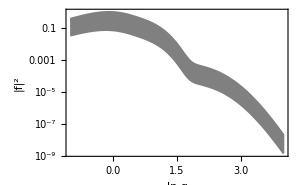
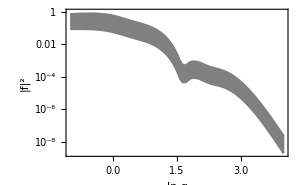
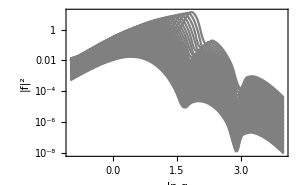

```mathematica
{ListLogPlot[#[[2]],DataRange->#[[1,2]],PlotStyle->Gray,Joined->True,InterpolationOrder->2,ImageSize->300,FrameLabel->{"ln q","|f|^2"}]&[fsqtable["Ar3p32FullAlt"]],
ListLogPlot[#[[2]],DataRange->#[[1,2]],PlotStyle->Gray,Joined->True,InterpolationOrder->2,ImageSize->300,FrameLabel->{"ln q","|f|^2"}]&[fsqtable["Ar3p12FullAlt"]],
ListLogPlot[#[[2]],DataRange->#[[1,2]],PlotStyle->Gray,Joined->True,InterpolationOrder->2,ImageSize->300,FrameLabel->{"ln q","|f|^2"}]&[fsqtable["Ar3sFullAlt"]]}
```

```mathematica
(* convert energies:*)
With[{lnk=-2.4 (* minimum simulated*)},
Print["Energy = ",ⅇ^(2(lnk))13.6," eV"]]
With[{lnk=1.8 (* maximum simulated *)},
Print["Energy = ",ⅇ^(2(lnk))13.6," eV"]]
```

Energy = 0.111925 eV

Energy = 497.736 eV

k'/αm_e = 0.173774

E_R = 0.410684 eV

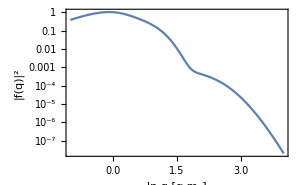

```mathematica
Block[{level="Ar3p32FullAlt",Nk=(*5*)14,lnkmin=-2.4,δlnk=0.05},
Print["k'/αm_e = ",ⅇ^(lnkmin+(Nk-1)δlnk)];
Print["E_R = ",ⅇ^(2(lnkmin+(Nk-1)δlnk))13.6, " eV"];ListLogPlot[#[[2,Nk]],DataRange->#[[1,2]],PlotRange->{All,All},PlotStyle->Automatic,Joined->True,InterpolationOrder->2,ImageSize->300,FrameLabel->{"ln q [α m_e]","|f(q)|^2"},Background->White]&[fsqtable[level]]]
```